```mathematica
EmbedGraphInPlantri8b[key_]:=Block[{val=allGraphs5[key], sets, reference={1,2,3,4,5}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ plantri8,14];
g=EdgeDelete[ g,{1<->2,2<->3,3<->4,4<->5,5<->1}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
Table[ChromaticPolynomial[EmbedGraphInPlantri8b[k],4],{k,alfa1s}]
```

{72,192,0,192,72}

```mathematica
Table[PlanarGraphQ[EmbedGraphInPlantri8b[k]],{k,alfa1s}]
```

{False,False,False,False,False}

```mathematica
alfa1s
```

{36166,31738,29608,36112,31714}

```mathematica
Table[ShowGraph5Least[k],{k,alfa1s}]
```

{-Graphics-361660,-Graphics-317380,-Graphics-296080,-Graphics-361120,-Graphics-317140}

```mathematica
ChromaticPolynomial[EmbedGraphInPlantri8b[29608],4]
```

0

```mathematica
emb=EmbedGraphInPlantri8b[29608]
```

```mathematica
emb2=EmbedGraphInPlantri8b[31714]
```

```mathematica
FindClique[emb]
```

{{12,13,7}}

```mathematica
FindClique[emb2]
```

{{11,16,1,3}}

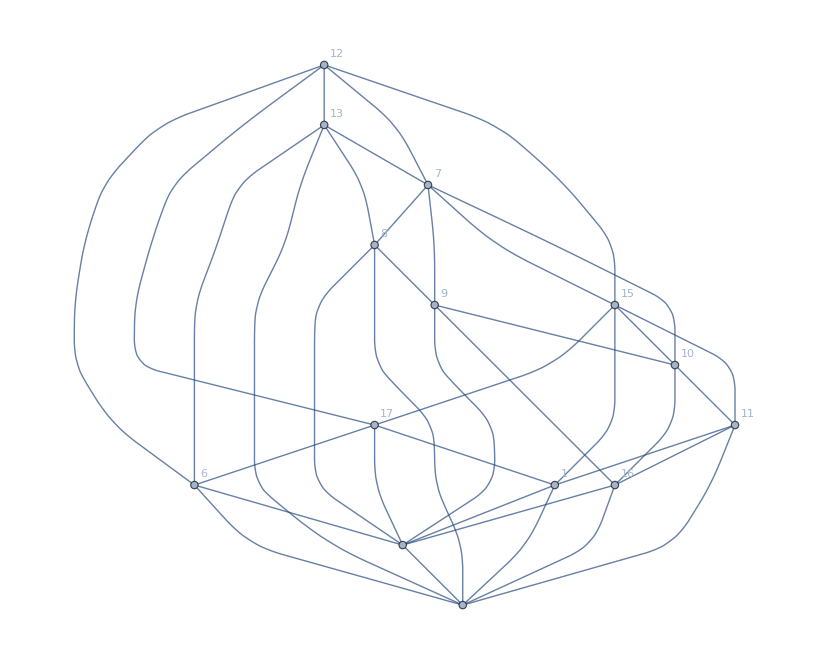

```mathematica
Graph[emb,GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
FindFullFormula5[emb]//Length
```

1586

```mathematica
1586/120
```

793/60

```mathematica
ChromaticPolynomial[EmbedGraphInPlantri8b[29608],5]/120
```

1586

```mathematica
CompleteBaseCoeff[ ChromaticPolynomial[emb,x]]
```

{0,0,0,0,0,1586,33088,146892,231967,163709,57997,10874,1080,53,1}

```mathematica
Length[Subsets[VertexList[emb],{5}]]
```

2002

```mathematica
VertexCount[emb]
```

14

```mathematica
EdgeCount[emb]
```

38

```mathematica
3*14-6
```

36

```mathematica
TableForm[
Monitor[
Table[
With[{emb=EmbedGraphInPlantri8b[k]},
Table[EdgeCount[Subgraph[emb,vert]],{vert,Subsets[VertexList[emb],{8}]}]//Tally//Sort
],
{k,alfa1s}
],
{k,vert}
],TableDepth->2
]
```

{7,7} | {8,67} | {9,179} | {10,452} | {11,681} | {12,675} | {13,529} | {14,292} | {15,100} | {16,17} | {17,4}
{8,29} | {9,180} | {10,463} | {11,701} | {12,767} | {13,503} | {14,245} | {15,97} | {16,15} | {17,3} | 
{8,36} | {9,135} | {10,472} | {11,740} | {12,741} | {13,545} | {14,250} | {15,72} | {16,12} |  | 
{8,29} | {9,180} | {10,463} | {11,701} | {12,767} | {13,503} | {14,245} | {15,97} | {16,15} | {17,3} | 
{7,7} | {8,67} | {9,179} | {10,452} | {11,681} | {12,675} | {13,529} | {14,292} | {15,100} | {16,17} | {17,4}

```mathematica
With[{f1=FindFullFormula5[emb],f2=FindFullFormula5[emb2]},
{Length[f1],Length[f2],Length[Intersection[f1,f2]]}
]
```

{1586,1657,390}

```mathematica
FactorInteger[{1586,1657,390}]
```

{{{2,1},{13,1},{61,1}},{{1657,1}},{{2,1},{3,1},{5,1},{13,1}}}

```mathematica
With[
{graphs=Append[Join[alfa1s,quads],lambdaKey]},
Block[{forms=Monitor[Table[FindFullFormula4[EmbedGraphInPlantri8b[k]],{k,graphs}],k], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 20665
-Graphics-361660 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-317380 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-296080 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-361120 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-317140 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 3 | 0
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 11 | 0
-Graphics-206653 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 63

```mathematica
allGraphs5[alfa1Key,"vertexsets"]
```

{{1,3},{2,4},{5}}

```mathematica
Keys[allGraphs5[alfa1Key]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull,atleast,atleastwhy,embed,colofourgenerator,colotree}

```mathematica
EdgeUpgrade[sols_,key_]:=Block[{edges, result = sols},
edges=Select[allGraphs5[key,"vertexsets"],Length[#]==2&];
edges=Map[UndirectedEdge[#[[1]],#[[2]]]&,edges];
Table[
sols=Map[SymbolReplace[#,e]&,sols]
,{e,edges}
];
sols
]
```

```mathematica
No5[sols_]:=Map[FilterSymbolNot[#,{1,2,3,4,5}]&,sols]
```

```mathematica
SymbolReplace[v123,3<->4]
```

v1234

```mathematica
EmbedGraphInPlantri8b[alfa1Key]
```

```mathematica
IntegerDigits[VertexList[EmbedGraphInPlantri8b[alfa1Key]],32]
```

{{12},{13},{7},{15},{17},{6},{8},{9},{10},{11},{16},{5},{1},{2}}

```mathematica
FindFullFormula5[EmbedGraphInPlantri8b[alfa1Key]]
```

```mathematica
No5[EdgeUpgrade[FindFullFormula5[EmbedGraphInPlantri8b[alfa1Key]],alfa1Key]]//DeleteDuplicates
```

{v69fx7gx8ahxbdxc,v68fx7gx9bhxadxc,v69fx7gx8bhxadxc,v68ax7gx9bdhxcxf,v68fx7gx9bdhxaxc,v68fgx7bx9xadhxc,v68fgx7bx9dhxaxc,v68ax7gx9bhxcxdf,v69bx7gx8ahxcxdf,v68fgx7x9bhxadxc,v68fgx7bhx9xadxc,v68fgx7x9bdxahxc,v6fgx7x8ahx9bdxc,v68fx7gx9bdxahxc,v6fx7gx8ahx9bdxc,v68fx7ghx9bdxaxc,v68fgx7bhx9dxaxc,v68fgx7hx9bdxaxc,v68ax7x9bdhxcxfg,v6ax7x8fgx9bdhxc,v69bx7x8fgxadhxc,v68fgx7x9bxadhxc,v68fgx7x9bdhxaxc,v6fgx7x8ax9bdhxc,v68ax7gx9fxbdhxc,v68bx7gx9fxadhxc,v6ax7gx8fx9bdhxc,v69bx7gx8fxadhxc,v68fx7gx9bxadhxc,v69fx7gx8bxadhxc,v69fx7gx8axbdhxc,v6fx7gx8ax9bdhxc,v67bx8fgx9xadhxc,v67bx8fgx9dhxaxc,v67x8fgx9bdhxaxc,v67gx8fx9bdhxaxc,v68ax7x9bhxcxdfg,v69bx7x8ahxcxdfg,v68ax7gx9dfxbhxc,v68bx7gx9dfxahxc,v6bx7gx8ahx9dfxc,v6ax7gx8bhx9dfxc,v67bx8ahx9dfxcxg,v67bx8ahx9xcxdfg,v67gx8bhx9dfxaxc,v67bx8ghx9dfxaxc,v68ax7bhx9dfxcxg,v68ax7bhx9xcxdfg,v68bx7ghx9dfxaxc,v68gx7bhx9dfxaxc,v69fx7bx8ahxcxdg,v67gx8ahx9fxbdxc,v68ax7ghx9fxbdxc,v69fx7ghx8axbdxc,v68fgx7bx9hxadxc,v69fx7bx8ghxadxc,v67gx8bhx9fxadxc,v67bx8ghx9fxadxc,v67x8fgx9bhxadxc,v67gx8fx9bhxadxc,v67bx8fgx9hxadxc,v68bx7ghx9fxadxc,v68gx7bhx9fxadxc,v69bx7hx8fgxadxc,v69bx7ghx8fxadxc,v69x7bhx8fgxadxc,v68fx7ghx9bxadxc,v69fx7bhx8gxadxc,v68fgx7hx9bxadxc,v69fx7ghx8bxadxc,v68fgx7bx9dxahxc,v6fgx7bx8ahx9dxc,v67gx8ahx9bdxcxf,v68ax7ghx9bdxcxf,v68ax7bx9dhxcxfg,v68ax7bx9fxcxdgh,v68gx7bx9fxadhxc,v6ax7bx8fgx9dhxc,v69x7bx8fgxadhxc,v69fx7bx8gxadhxc,v69fx7bx8axcxdgh,v6fgx7bx8ax9dhxc,v67gx8ax9bdhxcxf,v68ax7bx9dfxcxgh,v68gx7bx9dfxahxc,v68ax7bx9hxcxdfg,v6gx7bx8ahx9dfxc,v6ax7bx8ghx9dfxc,v69x7bx8ahxcxdfg,v67gx8ax9bhxcxdf,v67gx8ahx9dfxbxc,v67gx8ahx9bxcxdf,v69bx7ghx8axcxdf,v68ax7ghx9dfxbxc,v68ax7ghx9bxcxdf,v69fx7bx8ahxcgxd,v67bx8ahx9fxcgxd,v68ax7bhx9fxcgxd,v69fx7bhx8axcgxd,v69fx7x8ahxbdxcg,v67x8ahx9fxbdxcg,v68ax7hx9fxbdxcg,v69fx7hx8axbdxcg,v68fx7x9bhxadxcg,v69fx7x8bhxadxcg,v68fx7bx9hxadxcg,v69fx7bx8hxadxcg,v67x8bhx9fxadxcg,v67bx8hx9fxadxcg,v67x8fx9bhxadxcg,v67bx8fx9hxadxcg,v68bx7hx9fxadxcg,v68x7bhx9fxadxcg,v69bx7hx8fxadxcg,v69x7bhx8fxadxcg,v69fx7bhx8xadxcg,v68fx7bhx9xadxcg,v68fx7hx9bxadxcg,v69fx7hx8bxadxcg,v68fx7x9bdxahxcg,v6fx7x8ahx9bdxcg,v68fx7bx9dxahxcg,v6fx7bx8ahx9dxcg,v67bx8ahx9dxcgxf,v67x8ahx9bdxcgxf,v68ax7bhx9dxcgxf,v68ax7hx9bdxcgxf,v68fx7bhx9dxaxcg,v68fx7hx9bdxaxcg,v68ax7x9bdhxcgxf,v68fx7x9bdhxaxcg,v68ax7x9fxbdhxcg,v68bx7x9fxadhxcg,v6ax7x8fx9bdhxcg,v69bx7x8fxadhxcg,v68fx7x9bxadhxcg,v69fx7x8bxadhxcg,v69fx7x8axbdhxcg,v6fx7x8ax9bdhxcg,v68ax7bx9dhxcgxf,v68ax7bx9fxcgxdh,v68x7bx9fxadhxcg,v6ax7bx8fx9dhxcg,v69x7bx8fxadhxcg,v69fx7bx8xadhxcg,v68fx7bx9xadhxcg,v68fx7bx9dhxaxcg,v69fx7bx8axcgxdh,v6fx7bx8ax9dhxcg,v67bx8ax9dhxcgxf,v67x8ax9bdhxcgxf,v67bx8fx9dhxaxcg,v67x8fx9bdhxaxcg,v68ax7x9bhxcgxdf,v69bx7x8ahxcgxdf,v68ax7x9dfxbhxcg,v68bx7x9dfxahxcg,v6bx7x8ahx9dfxcg,v6ax7x8bhx9dfxcg,v68ax7bx9dfxcgxh,v68x7bx9dfxahxcg,v68ax7bx9hxcgxdf,v6x7bx8ahx9dfxcg,v6ax7bx8hx9dfxcg,v69x7bx8ahxcgxdf,v67x8ax9bhxcgxdf,v67bx8ax9hxcgxdf,v67bx8ahx9xcgxdf,v67x8ahx9dfxbxcg,v67x8bhx9dfxaxcg,v67bx8hx9dfxaxcg,v67bx8ahx9dfxcg,v67x8ahx9bxcgxdf,v69bx7hx8axcgxdf,v69x7bhx8axcgxdf,v68ax7bhx9xcgxdf,v68ax7hx9dfxbxcg,v68bx7hx9dfxaxcg,v68x7bhx9dfxaxcg,v68ax7bhx9dfxcg,v68ax7hx9bxcgxdf,v69fx7gx8ahxbcxd,v69fx7x8ahxbcxdg,v68fgx7x9hxadxbc,v69fx7x8ghxadxbc,v68fx7gx9hxadxbc,v69fx7gx8hxadxbc,v68fx7ghx9xadxbc,v68fgx7hx9xadxbc,v68fgx7x9dxahxbc,v6fgx7x8ahx9dxbc,v68fx7gx9dxahxbc,v6fx7gx8ahx9dxbc,v68fx7ghx9dxaxbc,v68fgx7hx9dxaxbc,v68fgx7x9xadhxbc,v68fgx7x9dhxaxbc,v68ax7x9dhxbcxfg,v68ax7x9fxbcxdgh,v68gx7x9fxadhxbc,v6ax7x8fgx9dhxbc,v69x7x8fgxadhxbc,v69fx7x8gxadhxbc,v69fx7x8axbcxdgh,v6fgx7x8ax9dhxbc,v68ax7gx9dhxbcxf,v68ax7gx9fxbcxdh,v68x7gx9fxadhxbc,v6ax7gx8fx9dhxbc,v69x7gx8fxadhxbc,v69fx7gx8xadhxbc,v68fx7gx9xadhxbc,v68fx7gx9dhxaxbc,v69fx7gx8axbcxdh,v6fx7gx8ax9dhxbc,v67x8fgx9dhxaxbc,v67gx8fx9dhxaxbc,v67x8fgx9xadhxbc,v67gx8fx9xadhxbc,v68ax7x9dfxbcxgh,v68gx7x9dfxahxbc,v68ax7x9hxbcxdfg,v6gx7x8ahx9dfxbc,v6ax7x8ghx9dfxbc,v69x7x8ahxbcxdfg,v68ax7gx9dfxbcxh,v68x7gx9dfxahxbc,v68ax7gx9hxbcxdf,v6x7gx8ahx9dfxbc,v6ax7gx8hx9dfxbc,v69x7gx8ahxbcxdf,v67x8ahx9dfxbcxg,v67x8ghx9dfxaxbc,v67gx8hx9dfxaxbc,v67gx8ahx9dfxbc,v67gx8ahx9xbcxdf,v67x8ahx9xbcxdfg,v68ax7hx9dfxbcxg,v68gx7hx9dfxaxbc,v68x7ghx9dfxaxbc,v68ax7ghx9dfxbc,v68ax7ghx9xbcxdf,v68ax7hx9xbcxdfg,v68fx7gx9bhxacxd,v69fx7gx8bhxacxd,v68fgx7bx9hxacxd,v69fx7bx8ghxacxd,v68fgx7x9bhxacxd,v67gx8bhx9fxacxd,v67bx8ghx9fxacxd,v67x8fgx9bhxacxd,v67gx8fx9bhxacxd,v67bx8fgx9hxacxd,v68bx7ghx9fxacxd,v68gx7bhx9fxacxd,v69bx7hx8fgxacxd,v69bx7ghx8fxacxd,v69x7bhx8fgxacxd,v68fx7ghx9bxacxd,v68fgx7bhx9xacxd,v69fx7bhx8gxacxd,v68fgx7hx9bxacxd,v69fx7ghx8bxacxd,v68fx7x9bhxacxdg,v69fx7x8bhxacxdg,v68fx7bx9hxacxdg,v69fx7bx8hxacxdg,v68fx7bhx9xacxdg,v68fgx7x9hxacxbd,v69fx7x8ghxacxbd,v68fx7gx9hxacxbd,v69fx7gx8hxacxbd,v67x8ghx9fxacxbd,v67gx8hx9fxacxbd,v67x8fgx9hxacxbd,v67gx8fx9hxacxbd,v68gx7hx9fxacxbd,v68x7ghx9fxacxbd,v69x7hx8fgxacxbd,v69x7ghx8fxacxbd,v69fx7ghx8xacxbd,v68fx7ghx9xacxbd,v68fgx7hx9xacxbd,v69fx7hx8gxacxbd,v68fgx7x9bdxacxh,v68fx7x9bdxacxgh,v68fgx7x9dxacxbh,v6fgx7x8bhx9dxac,v6fx7x8ghx9bdxac,v6fgx7x8hx9bdxac,v68fx7gx9bdxacxh,v68fx7gx9dxacxbh,v6fx7gx8bhx9dxac,v6fx7gx8hx9bdxac,v68fgx7bx9dxacxh,v68fx7bx9dxacxgh,v6fx7bx8ghx9dxac,v6fgx7bx8hx9dxac,v67gx8bhx9dxacxf,v67bx8ghx9dxacxf,v67x8ghx9bdxacxf,v67gx8hx9bdxacxf,v68bx7ghx9dxacxf,v68gx7bhx9dxacxf,v68gx7hx9bdxacxf,v68x7ghx9bdxacxf,v68fx7bhx9dxacxg,v68fx7hx9bdxacxg,v68fx7ghx9dxacxb,v68fx7ghx9bdxac,v68fgx7bhx9dxac,v68fgx7hx9bdxac,v68fgx7hx9dxacxb,v68fx7x9bdhxacxg,v68fgx7x9dhxacxb,v68gx7x9bdhxacxf,v68bx7x9dhxacxfg,v68x7x9bdhxacxfg,v68bx7x9fxacxdgh,v68gx7x9fxacxbdh,v6x7x8fgx9bdhxac,v6gx7x8fx9bdhxac,v6bx7x8fgx9dhxac,v69bx7x8fgxacxdh,v69bx7x8fxacxdgh,v69x7x8fgxacxbdh,v6fgx7x8x9bdhxac,v68fx7x9bxacxdgh,v68fgx7x9xacxbdh,v69fx7x8gxacxbdh,v68fgx7x9bdhxac,v6fx7x8gx9bdhxac,v68fgx7x9bxacxdh,v6fgx7x8bx9dhxac,v69fx7x8bxacxdgh,v68bx7gx9dhxacxf,v68x7gx9bdhxacxf,v68bx7gx9fxacxdh,v68x7gx9fxacxbdh,v6x7gx8fx9bdhxac,v6bx7gx8fx9dhxac,v69bx7gx8fxacxdh,v69x7gx8fxacxbdh,v69fx7gx8xacxbdh,v6fx7gx8x9bdhxac,v68fx7gx9dhxacxb,v68fx7gx9xacxbdh,v68fx7gx9bdhxac,v68fx7gx9bxacxdh,v69fx7gx8bxacxdh,v6fx7gx8bx9dhxac,v68gx7bx9dhxacxf,v68x7bx9dhxacxfg,v68gx7bx9fxacxdh,v68x7bx9fxacxdgh,v6x7bx8fgx9dhxac,v6gx7bx8fx9dhxac,v69x7bx8fgxacxdh,v69x7bx8fxacxdgh,v6fgx7bx8x9dhxac,v69fx7bx8xacxdgh,v68fx7bx9dhxacxg,v68fx7bx9xacxdgh,v68fgx7bx9xacxdh,v69fx7bx8gxacxdh,v68fgx7bx9dhxac,v6fx7bx8gx9dhxac,v67gx8x9bdhxacxf,v67bx8gx9dhxacxf,v67x8gx9bdhxacxf,v67gx8bx9dhxacxf,v67bx8fx9dhxacxg,v67x8fgx9dhxacxb,v67gx8fx9dhxacxb,v67bx8fgx9xacxdh,v67bx8fx9xacxdgh,v67x8fgx9xacxbdh,v67gx8fx9xacxbdh,v67bx8fgx9dhxac,v67x8fgx9bdhxac,v67gx8fx9bdhxac,v67x8fx9bdhxacxg,v68bx7x9dfxacxgh,v68gx7x9dfxacxbh,v68bx7x9hxacxdfg,v68gx7x9bhxacxdf,v68x7x9bhxacxdfg,v6gx7x8bhx9dfxac,v6bx7x8ghx9dfxac,v69bx7x8ghxacxdf,v69bx7x8hxacxdfg,v69x7x8bhxacxdfg,v68bx7gx9dfxacxh,v68x7gx9dfxacxbh,v68bx7gx9hxacxdf,v68x7gx9bhxacxdf,v6x7gx8bhx9dfxac,v6bx7gx8hx9dfxac,v69bx7gx8hxacxdf,v69x7gx8bhxacxdf,v68gx7bx9dfxacxh,v68x7bx9dfxacxgh,v68gx7bx9hxacxdf,v68x7bx9hxacxdfg,v6x7bx8ghx9dfxac,v6gx7bx8hx9dfxac,v69x7bx8ghxacxdf,v69x7bx8hxacxdfg,v67gx8x9bhxacxdf,v67x8gx9bhxacxdf,v67bx8gx9hxacxdf,v67gx8bx9hxacxdf,v67x8bhx9dfxacxg,v67bx8hx9dfxacxg,v67x8ghx9dfxacxb,v67gx8hx9dfxacxb,v67gx8bhx9xacxdf,v67x8bhx9xacxdfg,v67bx8ghx9xacxdf,v67bx8hx9xacxdfg,v67gx8bhx9dfxac,v67bx8ghx9dfxac,v67x8ghx9bxacxdf,v67gx8hx9bxacxdf,v69bx7ghx8xacxdf,v69bx7hx8gxacxdf,v69x7bhx8gxacxdf,v69x7ghx8bxacxdf,v68bx7hx9dfxacxg,v68x7bhx9dfxacxg,v68gx7hx9dfxacxb,v68x7ghx9dfxacxb,v68bx7ghx9xacxdf,v68bx7hx9xacxdfg,v68gx7bhx9xacxdf,v68x7bhx9xacxdfg,v68bx7ghx9dfxac,v68gx7bhx9dfxac,v68gx7hx9bxacxdf,v68x7ghx9bxacxdf,v68fgx7bx9cxahxd,v6fgx7bx8ahx9cxd,v68fgx7x9bcxahxd,v6fgx7x8ahx9bcxd,v68fx7gx9bcxahxd,v6fx7gx8ahx9bcxd,v67bx8ahx9cxdxfg,v67bx8fgx9cxahxd,v68ax7bhx9cxdxfg,v6ax7bhx8fgx9cxd,v68fx7ghx9bcxaxd,v68fgx7bhx9cxaxd,v68fgx7hx9bcxaxd,v6fgx7bhx8ax9cxd,v68fx7bx9cxahxdg,v6fx7bx8ahx9cxdg,v67bx8ahx9cxdgxf,v68ax7bhx9cxdgxf,v68fx7bhx9cxaxdg,v68fgx7x9cxahxbd,v6fgx7x8ahx9cxbd,v68fx7gx9cxahxbd,v6fx7gx8ahx9cxbd,v67gx8ahx9cxbdxf,v67x8ahx9cxbdxfg,v67x8fgx9cxahxbd,v67gx8fx9cxahxbd,v68ax7ghx9cxbdxf,v68ax7hx9cxbdxfg,v6ax7hx8fgx9cxbd,v6ax7ghx8fx9cxbd,v68fx7ghx9cxaxbd,v68fgx7hx9cxaxbd,v6fgx7hx8ax9cxbd,v6fx7ghx8ax9cxbd,v68fgx7x9cxadxbh,v6fgx7x8bhx9cxad,v68fgx7x9bcxadxh,v68fx7x9bcxadxgh,v6fx7x8ghx9bcxad,v6fgx7x8hx9bcxad,v68fx7gx9bcxadxh,v68fx7gx9cxadxbh,v6fx7gx8bhx9cxad,v6fx7gx8hx9bcxad,v68fgx7bx9cxadxh,v68fx7bx9cxadxgh,v6fx7bx8ghx9cxad,v6fgx7bx8hx9cxad,v67gx8bhx9cxadxf,v67bx8ghx9cxadxf,v67x8bhx9cxadxfg,v67bx8hx9cxadxfg,v67bx8fgx9cxadxh,v67bx8fx9cxadxgh,v67x8fgx9cxadxbh,v67gx8fx9cxadxbh,v68bx7ghx9cxadxf,v68gx7bhx9cxadxf,v68bx7hx9cxadxfg,v68x7bhx9cxadxfg,v6x7bhx8fgx9cxad,v6gx7bhx8fx9cxad,v6bx7hx8fgx9cxad,v6bx7ghx8fx9cxad,v68fx7bhx9cxadxg,v68fx7hx9bcxadxg,v68fx7ghx9cxadxb,v6fgx7bhx8x9cxad,v68fx7ghx9bcxad,v68fgx7hx9cxadxb,v68fgx7bhx9cxad,v6fx7bhx8gx9cxad,v68fgx7hx9bcxad,v6fgx7hx8bx9cxad,v6fx7ghx8bx9cxad,v68fgx7x9cxadhxb,v68bx7x9cxadhxfg,v68ax7x9cxbdhxfg,v6bx7x8fgx9cxadh,v6ax7x8fgx9cxbdh,v68fx7x9bcxadhxg,v68fx7x9bcxaxdgh,v68fgx7x9cxaxbdh,v68fgx7x9bcxaxdh,v68fgx7x9bcxadh,v6fgx7x8bx9cxadh,v6fgx7x8ax9cxbdh,v68gx7x9bcxadhxf,v68ax7x9bcxdghxf,v68ax7gx9cxbdhxf,v68ax7gx9bcxdhxf,v68bx7gx9cxadhxf,v68x7gx9bcxadhxf,v68fx7gx9cxadhxb,v68fx7gx9cxaxbdh,v68fx7gx9bcxaxdh,v68fx7gx9bcxadh,v68gx7bx9cxadhxf,v68ax7bx9cxdghxf,v68ax7bx9cxdhxfg,v68x7bx9cxadhxfg,v6x7bx8fgx9cxadh,v6gx7bx8fx9cxadh,v6ax7bx8fgx9cxdh,v6ax7bx8fx9cxdgh,v6fgx7bx8x9cxadh,v68fx7bx9cxadhxg,v68fx7bx9cxaxdgh,v68fgx7bx9cxaxdh,v68fgx7bx9cxadh,v6fx7bx8gx9cxadh,v6fgx7bx8ax9cxdh,v6fx7bx8ax9cxdgh,v67bx8gx9cxadhxf,v67gx8bx9cxadhxf,v67bx8ax9cxdghxf,v67gx8ax9cxbdhxf,v67x8fgx9cxadhxb,v67gx8fx9cxadhxb,v67bx8fgx9cxaxdh,v67bx8fx9cxaxdgh,v67x8fgx9cxaxbdh,v67gx8fx9cxaxbdh,v67bx8fgx9cxadh,v68ax7x9cxbhxdfg,v68bx7x9cxahxdfg,v6bx7x8ahx9cxdfg,v6ax7x8bhx9cxdfg,v68ax7x9bcxdfxgh,v68gx7x9bcxahxdf,v6gx7x8ahx9bcxdf,v6ax7x8ghx9bcxdf,v68ax7gx9bcxdfxh,v68ax7gx9cxbhxdf,v68bx7gx9cxahxdf,v68x7gx9bcxahxdf,v6x7gx8ahx9bcxdf,v6bx7gx8ahx9cxdf,v6ax7gx8bhx9cxdf,v6ax7gx8hx9bcxdf,v68ax7bx9cxdfgxh,v68ax7bx9cxdfxgh,v68gx7bx9cxahxdf,v68x7bx9cxahxdfg,v6x7bx8ahx9cxdfg,v6gx7bx8ahx9cxdf,v6ax7bx8ghx9cxdf,v6ax7bx8hx9cxdfg,v67bx8ax9cxdfxgh,v67gx8ax9cxbhxdf,v67bx8gx9cxahxdf,v67gx8bx9cxahxdf,v67bx8ahx9cxdfxg,v67x8ahx9bcxdfxg,v67gx8ahx9cxbxdf,v67x8ahx9cxbxdfg,v67gx8bhx9cxaxdf,v67x8bhx9cxaxdfg,v67bx8ghx9cxaxdf,v67bx8hx9cxaxdfg,v67x8ghx9bcxaxdf,v67gx8hx9bcxaxdf,v67bx8ahx9cxdfg,v67gx8ahx9bcxdf,v6gx7bhx8ax9cxdf,v6bx7ghx8ax9cxdf,v6ax7bhx8gx9cxdf,v6ax7ghx8bx9cxdf,v68ax7bhx9cxdfxg,v68ax7hx9bcxdfxg,v68ax7ghx9cxbxdf,v68ax7hx9cxbxdfg,v68bx7ghx9cxaxdf,v68bx7hx9cxaxdfg,v68gx7bhx9cxaxdf,v68x7bhx9cxaxdfg,v68gx7hx9bcxaxdf,v68x7ghx9bcxaxdf,v68ax7bhx9cxdfg,v68ax7ghx9bcxdf,v6fgx7x8acx9bhxd,v69fx7gx8acxbhxd,v69fx7gx8bcxahxd,v6fx7gx8acx9bhxd,v69fx7bhx8acxdxg,v6fgx7bhx8acx9xd,v69fx7bhx8cgxaxd,v69fx7ghx8bcxaxd,v69fx7x8acxbdxgh,v69fx7x8cgxahxbd,v6fgx7x8acx9hxbd,v69fx7gx8acxbdxh,v69fx7gx8cxahxbd,v6fx7gx8acx9hxbd,v69fx7hx8acxbdxg,v69fx7ghx8cxaxbd,v69fx7hx8cgxaxbd,v69fx7ghx8acxbd,v6fgx7hx8acx9xbd,v6fx7ghx8acx9xbd,v69fx7x8bcxadxgh,v69fx7x8cgxadxbh,v6fgx7x8cx9bhxad,v6fx7x8cgx9bhxad,v6fgx7x8bcx9hxad,v69fx7gx8bcxadxh,v69fx7gx8cxadxbh,v6fx7gx8cx9bhxad,v6fx7gx8bcx9hxad,v69fx7bhx8cxadxg,v69fx7hx8bcxadxg,v6fgx7bhx8cx9xad,v6fx7bhx8cgx9xad,v6fgx7hx8bcx9xad,v6fx7ghx8bcx9xad,v69fx7bhx8cgxad,v69fx7ghx8bcxad,v69fx7x8acxbdhxg,v69fx7x8bcxadhxg,v6fgx7x8acx9xbdh,v6fgx7x8bcx9xadh,v69fx7x8cgxaxbdh,v6fgx7x8bcx9dhxa,v69fx7x8bcxaxdgh,v6fx7x8acx9bdhxg,v6fgx7x8cx9bdhxa,v6fx7x8cgx9bdhxa,v6fgx7x8acx9bdh,v6gx7x8acx9bdhxf,v6ax7x8cgx9bdhxf,v69bx7x8acxdghxf,v69bx7x8cgxadhxf,v69fx7x8acxbxdgh,v69fx7x8cgxadhxb,v6fgx7x8acx9dhxb,v6x7gx8acx9bdhxf,v6bx7gx8acx9dhxf,v6ax7gx8bcx9dhxf,v6ax7gx8cx9bdhxf,v69bx7gx8cxadhxf,v69x7gx8bcxadhxf,v69bx7gx8acxdhxf,v69x7gx8acxbdhxf,v69fx7gx8cxadhxb,v69fx7gx8acxbxdh,v69fx7gx8cxaxbdh,v69fx7gx8bcxaxdh,v69fx7gx8acxbdh,v69fx7gx8bcxadh,v6fx7gx8acx9dhxb,v6fx7gx8bcx9dhxa,v6fx7gx8acx9bdh,v6fx7gx8cx9bdhxa,v69fx7bx8cxadhxg,v69fx7bx8acxdhxg,v69fx7bx8cxaxdgh,v69fx7bx8cgxaxdh,v69fx7bx8acxdgh,v69fx7bx8cgxadh,v6fx7bx8acx9dhxg,v6fgx7bx8cx9dhxa,v6fx7bx8cgx9dhxa,v6fgx7bx8acx9dh,v6fgx7bx8cx9xadh,v6fx7bx8cgx9xadh,v6fgx7bx8acx9xdh,v6fx7bx8acx9xdgh,v67bx8acx9dhxfxg,v67bx8acx9xdghxf,v67bx8cgx9xadhxf,v67gx8acx9xbdhxf,v67gx8bcx9xadhxf,v67bx8cgx9dhxaxf,v67gx8bcx9dhxaxf,v67x8acx9bdhxfxg,v67gx8cx9bdhxaxf,v67x8cgx9bdhxaxf,v67gx8acx9bdhxf,v69bx7x8acxdfxgh,v69bx7x8cgxahxdf,v6gx7x8acx9bhxdf,v6ax7x8cgx9bhxdf,v69bx7gx8acxdfxh,v69x7gx8acxbhxdf,v69bx7gx8cxahxdf,v69x7gx8bcxahxdf,v6x7gx8acx9bhxdf,v6bx7gx8acx9hxdf,v6ax7gx8cx9bhxdf,v6ax7gx8bcx9hxdf,v67bx8acx9xdfxgh,v67gx8acx9xbhxdf,v67bx8cgx9xahxdf,v67gx8bcx9xahxdf,v67x8acx9bhxdfxg,v67bx8acx9hxdfxg,v67gx8cx9bhxaxdf,v67x8cgx9bhxaxdf,v67bx8cgx9hxaxdf,v67gx8bcx9hxaxdf,v67gx8acx9bhxdf,v6gx7bhx8acx9xdf,v6bx7ghx8acx9xdf,v6ax7bhx8cgx9xdf,v6ax7ghx8bcx9xdf,v69bx7hx8acxdfxg,v69x7bhx8acxdfxg,v69bx7ghx8cxaxdf,v69bx7hx8cgxaxdf,v69x7bhx8cgxaxdf,v69x7ghx8bcxaxdf,v69bx7ghx8acxdf}

```mathematica
Length[%]
```

753

```mathematica
EdgeUpgrade[FindFullFormula5[EmbedGraphInPlantri8b[alfa1Key]],alfa1Key]
```

{v137gx24bdx58ahx69fxc,v137gx24bdx569fx8ahxc,v137gx24adx568fx9bhxc,v137gx24adx569fx8bhxc,v137gx24fx568ax9bdhxc,v137gx24ax568fx9bdhxc,v139x247bx5adhx68fgxc,v13ax247bx59dhx68fgxc,v137gx24dfx568ax9bhxc,v137gx24dfx58ahx69bxc,v137gx24cx58ahx69fxbd,v137gx24cx569fx8ahxbd,v137x24cx5adx68fgx9bh,v137gx24cx5adx68fx9bh,v137gx24cx568fx9bhxad,v137gx24cx5adx69fx8bh,v137gx24cx569fx8bhxad,v139x24cx5adx68fgx7bh,v137x24cx5ahx68fgx9bd,v137x24cx58ahx6fgx9bd,v137gx24cx5ahx68fx9bd,v137gx24cx568fx9bdxah,v137gx24cx56fx8ahx9bd,v137gx24cx58ahx6fx9bd,v13ax24cx568fx7ghx9bd,v13ax24cx59dx68fgx7bh,v13ax24cx57hx68fgx9bd,v137x24cx568ax9bdhxfg,v137x24cx56ax8fgx9bdh,v137x24cx5adhx69bx8fg,v137x24cx5adhx68fgx9b,v137x24cx5ax68fgx9bdh,v137x24cx58ax6fgx9bdh,v13ax24cx57x68fgx9bdh,v137gx24cx568ax9bdhxf,v137gx24cx5fx68ax9bdh,v137gx24cx59fx68axbdh,v137gx24cx59fx68bxadh,v137gx24cx5adhx68bx9f,v137gx24cx568ax9fxbdh,v137gx24cx56ax8fx9bdh,v137gx24cx58fx6ax9bdh,v137gx24cx58fx69bxadh,v137gx24cx5adhx69bx8f,v137gx24cx5adhx68fx9b,v137gx24cx5ax68fx9bdh,v137gx24cx568fx9bdhxa,v137gx24cx568fx9bxadh,v13ax24cx568fx7gx9bdh,v137gx24cx5adhx69fx8b,v137gx24cx569fx8bxadh,v137gx24cx58ax69fxbdh,v137gx24cx569fx8axbdh,v137gx24cx58ax6fx9bdh,v137gx24cx56fx8ax9bdh,v139x24cx5adhx68fgx7b,v13ax24cx59dhx68fgx7b,v139x24cx5adhx67bx8fg,v13ax24cx59dhx67bx8fg,v13ax24cx567x8fgx9bdh,v13ax24cx58fx67gx9bdh,v137x24cx568ax9bhxdfg,v137x24cx58ahx69bxdfg,v137gx24cx568ax9dfxbh,v137gx24cx59dfx68axbh,v137gx24cx5ahx68bx9df,v137gx24cx59dfx68bxah,v137gx24cx5dfx68ax9bh,v137gx24cx568ax9bhxdf,v137gx24cx58ahx6bx9df,v137gx24cx59dfx6bx8ah,v137gx24cx56ax8bhx9df,v137gx24cx59dfx6ax8bh,v137gx24cx5dfx69bx8ah,v137gx24cx58ahx69bxdf,v13gx24cx58ahx67bx9df,v139x24cx58ahx67bxdfg,v13gx24cx59dfx67bx8ah,v13ax24cx59dfx67gx8bh,v13ax24cx59dfx67bx8gh,v13gx24cx568ax7bhx9df,v139x24cx568ax7bhxdfg,v13gx24cx59dfx68ax7bh,v13ax24cx59dfx68bx7gh,v13ax24cx59dfx68gx7bh,v13cx247bx58ahx69fxdg,v13cx247bx569fx8ahxdg,v13cx24bdx58ahx69fx7g,v13cx24bdx569fx7gx8ah,v13cx24bdx59fx67gx8ah,v13cx24bdx58ahx67gx9f,v13cx24bdx59fx68ax7gh,v13cx24bdx568ax7ghx9f,v13cx24bdx58ax69fx7gh,v13cx24bdx569fx7ghx8a,v13cx247x5adx68fgx9bh,v13cx24adx57x68fgx9bh,v13cx24adx568fx7gx9bh,v13cx24adx569fx7gx8bh,v13cx247bx59hx68fgxad,v13cx24adx59hx68fgx7b,v13cx247bx5adx68fgx9h,v13cx247bx5adx69fx8gh,v13cx247bx569fx8ghxad,v13cx24adx569fx7bx8gh,v13cx24adx59fx67gx8bh,v13cx24adx59fx67bx8gh,v13cx24adx567x8fgx9bh,v13cx24adx58fx67gx9bh,v13cx24adx59hx67bx8fg,v13cx24adx59fx68bx7gh,v13cx24adx59fx68gx7bh,v13cx24adx57hx69bx8fg,v13cx24adx58fx69bx7gh,v13cx24adx569x7bhx8fg,v13cx24adx568fx7ghx9b,v13cx24adx569fx7bhx8g,v13cx24adx59x68fgx7bh,v13cx24adx57hx68fgx9b,v13cx24adx569fx7ghx8b,v13cx247x5ahx68fgx9bd,v13cx247x58ahx6fgx9bd,v13cx247bx5ahx68fgx9d,v13cx247bx59dx68fgxah,v13cx247bx59dx6fgx8ah,v13cx247bx58ahx6fgx9d,v13cx24fx58ahx67gx9bd,v13cx24fx568ax7ghx9bd,v13cx24ax568fx7ghx9bd,v13cx24ax59dx68fgx7bh,v13cx24ax57hx68fgx9bd,v13cx247x568ax9bdhxfg,v13cx247x56ax8fgx9bdh,v13cx247x5adhx69bx8fg,v13cx247x5adhx68fgx9b,v13cx247x5ax68fgx9bdh,v13cx247x58ax6fgx9bdh,v13cx24ax57x68fgx9bdh,v13cx24fx568ax7gx9bdh,v13cx24ax568fx7gx9bdh,v13cx247bx568ax9dhxfg,v13cx247bx59dhx68axfg,v13cx247bx59fx68axdgh,v13cx247bx59fx68gxadh,v13cx247bx5adhx68gx9f,v13cx247bx568ax9fxdgh,v13cx247bx56ax8fgx9dh,v13cx247bx59dhx6ax8fg,v13cx247bx569x8fgxadh,v13cx247bx5adhx69x8fg,v13cx247bx5adhx68fgx9,v13cx247bx5adhx69fx8g,v13cx247bx5ax68fgx9dh,v13cx247bx59dhx68fgxa,v13cx247bx569fx8gxadh,v13cx247bx59x68fgxadh,v13cx24ax59dhx68fgx7b,v13cx247bx58ax69fxdgh,v13cx247bx58ax6fgx9dh,v13cx247bx59dhx6fgx8a,v13cx247bx569fx8axdgh,v13cx24fx58ax67gx9bdh,v13cx24ax59dhx67bx8fg,v13cx24ax567x8fgx9bdh,v13cx24ax58fx67gx9bdh,v13cx247x568ax9bhxdfg,v13cx247x58ahx69bxdfg,v13cx24dfx568ax7gx9bh,v13cx24dfx58ahx69bx7g,v13cx247bx568ax9dfxgh,v13cx247bx59dfx68axgh,v13cx247bx5ahx68gx9df,v13cx247bx59dfx68gxah,v13cx247bx59hx68axdfg,v13cx247bx568ax9hxdfg,v13cx247bx58ahx6gx9df,v13cx247bx59dfx6gx8ah,v13cx247bx56ax8ghx9df,v13cx247bx59dfx6ax8gh,v13cx247bx569x8ahxdfg,v13cx247bx58ahx69xdfg,v13cx24dfx58ax67gx9bh,v13cx24bx58ahx67gx9df,v13cx24bx59dfx67gx8ah,v13cx24ax59dfx67gx8bh,v13cx24ax59dfx67bx8gh,v13cx24dfx58ahx67gx9b,v13cx24dfx58ax69bx7gh,v13cx24bx568ax7ghx9df,v13cx24bx59dfx68ax7gh,v13cx24ax59dfx68bx7gh,v13cx24ax59dfx68gx7bh,v13cx24dfx568ax7ghx9b,v137gx24bdx5cx69fx8ah,v137x24adx5cx68fgx9bh,v137gx24adx5cx68fx9bh,v137gx24adx5cx69fx8bh,v139x24adx5cx68fgx7bh,v13ax247x5cx68fgx9bdh,v137x24ax5cx68fgx9bdh,v137gx24fx5cx68ax9bdh,v137gx24ax5cx68fx9bdh,v13ax247bx5cx68fgx9dh,v139x247bx5cx68fgxadh,v137gx24dfx5cx68ax9bh,v137gx24dfx5cx69bx8ah,v13cgx247bx58ahx69fxd,v13cgx247bx569fx8ahxd,v13cgx24dx58ahx69fx7b,v13cgx24dx569fx7bx8ah,v13cgx24dx59fx67bx8ah,v13cgx24dx58ahx67bx9f,v13cgx24dx59fx68ax7bh,v13cgx24dx568ax7bhx9f,v13cgx24dx58ax69fx7bh,v13cgx24dx569fx7bhx8a,v13cgx247bx5dx69fx8ah,v13cgx24bdx58ahx69fx7,v13cgx24bdx569fx7x8ah,v13cgx247x58ahx69fxbd,v13cgx247x569fx8ahxbd,v137x24bdx58ahx69fxcg,v137x24bdx569fx8ahxcg,v13cgx24bdx57x69fx8ah,v13cgx24bdx59fx67x8ah,v13cgx24bdx567x8ahx9f,v13cgx24bdx58ahx67x9f,v13cgx24bdx59fx68ax7h,v13cgx24bdx57hx68ax9f,v13cgx24bdx568ax7hx9f,v13cgx24bdx58ax69fx7h,v13cgx24bdx57hx69fx8a,v13cgx24bdx569fx7hx8a,v13cgx24adx568fx7x9bh,v13cgx24adx569fx7x8bh,v13cgx247x5adx68fx9bh,v13cgx247x568fx9bhxad,v13cgx247x5adx69fx8bh,v13cgx247x569fx8bhxad,v137x24adx568fx9bhxcg,v137x24adx569fx8bhxcg,v13cgx24adx57x68fx9bh,v13cgx24adx57x69fx8bh,v13cgx247bx59hx68fxad,v13cgx24adx59hx68fx7b,v13cgx247bx5adx68fx9h,v13cgx247bx568fx9hxad,v13cgx24adx568fx7bx9h,v13cgx247bx58hx69fxad,v13cgx24adx58hx69fx7b,v13cgx247bx5adx69fx8h,v13cgx247bx569fx8hxad,v13cgx24adx569fx7bx8h,v13cgx24adx59fx67x8bh,v13cgx24adx567x8bhx9f,v13cgx24adx58hx67bx9f,v13cgx24adx59fx67bx8h,v13cgx24adx58fx67x9bh,v13cgx24adx567x8fx9bh,v13cgx24adx59hx67bx8f,v13cgx24adx58fx67bx9h,v13cgx24adx59fx68bx7h,v13cgx24adx57hx68bx9f,v13cgx24adx568x7bhx9f,v13cgx24adx59fx68x7bh,v13cgx24adx58fx69bx7h,v13cgx24adx57hx69bx8f,v13cgx24adx569x7bhx8f,v13cgx24adx58fx69x7bh,v13cgx24adx569fx7bhx8,v13cgx24adx59x68fx7bh,v13cgx24adx57hx68fx9b,v13cgx24adx568fx7bhx9,v13cgx24adx58x69fx7bh,v139x24adx568fx7bhxcg,v13cgx24adx568fx7hx9b,v13cgx24adx57hx69fx8b,v13cgx24adx569fx7hx8b,v13cgx247x5ahx68fx9bd,v13cgx247x568fx9bdxah,v13cgx247x56fx8ahx9bd,v13cgx247x58ahx6fx9bd,v13cgx247bx5ahx68fx9d,v13cgx247bx59dx68fxah,v13cgx247bx568fx9dxah,v13cgx247bx56fx8ahx9d,v13cgx247bx59dx6fx8ah,v13cgx247bx58ahx6fx9d,v13cgx24fx59dx67bx8ah,v13cgx24fx567x8ahx9bd,v13cgx24fx58ahx67bx9d,v13cgx24fx58ahx67x9bd,v13cgx24fx59dx68ax7bh,v13cgx24fx57hx68ax9bd,v13cgx24fx568ax7bhx9d,v13cgx24fx568ax7hx9bd,v13cgx24ax59dx68fx7bh,v13cgx24ax57hx68fx9bd,v13cgx24ax568fx7bhx9d,v13cgx24ax568fx7hx9bd,v13cgx24fx568ax7x9bdh,v13cgx24ax568fx7x9bdh,v13cgx247x568ax9bdhxf,v13cgx247x5fx68ax9bdh,v13cgx247x59fx68axbdh,v13cgx247x59fx68bxadh,v13cgx247x5adhx68bx9f,v13cgx247x568ax9fxbdh,v13cgx247x56ax8fx9bdh,v13cgx247x58fx6ax9bdh,v13cgx247x58fx69bxadh,v13cgx247x5adhx69bx8f,v13cgx247x5adhx68fx9b,v13cgx247x5ax68fx9bdh,v13cgx247x568fx9bdhxa,v13cgx247x568fx9bxadh,v13ax247x568fx9bdhxcg,v13cgx247x5adhx69fx8b,v13cgx247x569fx8bxadh,v13cgx247x58ax69fxbdh,v13cgx247x569fx8axbdh,v13cgx247x58ax6fx9bdh,v13cgx247x56fx8ax9bdh,v137x24fx568ax9bdhxcg,v137x24ax568fx9bdhxcg,v13cgx24fx57x68ax9bdh,v13cgx24ax57x68fx9bdh,v13cgx247bx568ax9dhxf,v13cgx247bx59dhx68axf,v13cgx24fx568ax7bx9dh,v13cgx24fx59dhx68ax7b,v13cgx247bx5fx68ax9dh,v13cgx247bx59fx68axdh,v13cgx247bx5dhx68ax9f,v13cgx247bx568x9fxadh,v13cgx247bx59fx68xadh,v13cgx247bx568ax9fxdh,v13cgx247bx5adhx68x9f,v13cgx247bx56ax8fx9dh,v13cgx247bx58fx6ax9dh,v13cgx247bx59dhx6ax8f,v13cgx247bx569x8fxadh,v13cgx247bx58fx69xadh,v13cgx247bx5adhx69x8f,v13cgx247bx5adhx69fx8,v13cgx247bx569fx8xadh,v13cgx247bx5adhx68fx9,v13cgx247bx5ax68fx9dh,v139x247bx5adhx68fxcg,v13cgx247bx59dhx68fxa,v13cgx247bx59x68fxadh,v13cgx24ax59dhx68fx7b,v13ax247bx59dhx68fxcg,v13cgx247bx568fx9xadh,v13cgx247bx58x69fxadh,v13cgx247bx568fx9dhxa,v13cgx24ax568fx7bx9dh,v13ax247bx568fx9dhxcg,v139x247bx568fxadhxcg,v13cgx247bx58ax69fxdh,v13cgx247bx5dhx69fx8a,v13cgx247bx58ax6fx9dh,v13cgx247bx56fx8ax9dh,v13cgx247bx569fx8axdh,v13cgx247bx59dhx6fx8a,v13cgx24fx58ax67bx9dh,v13cgx24fx59dhx67bx8a,v13cgx24fx58ax67x9bdh,v13cgx24fx567x8ax9bdh,v13cgx24ax58fx67bx9dh,v13cgx24ax59dhx67bx8f,v13cgx24ax58fx67x9bdh,v13cgx24ax567x8fx9bdh,v13cgx24dfx568ax7x9bh,v13cgx24dfx58ahx69bx7,v13cgx247x568ax9dfxbh,v13cgx247x59dfx68axbh,v13cgx247x5ahx68bx9df,v13cgx247x59dfx68bxah,v13cgx247x5dfx68ax9bh,v13cgx247x568ax9bhxdf,v13cgx247x58ahx6bx9df,v13cgx247x59dfx6bx8ah,v13cgx247x56ax8bhx9df,v13cgx247x59dfx6ax8bh,v13cgx247x5dfx69bx8ah,v13cgx247x58ahx69bxdf,v137x24dfx568ax9bhxcg,v137x24dfx58ahx69bxcg,v13cgx24dfx57x68ax9bh,v13cgx24dfx57x69bx8ah,v13cgx247bx568ax9dfxh,v13cgx247bx59dfx68axh,v13cgx247bx5hx68ax9df,v13cgx247bx568x9dfxah,v13cgx247bx5ahx68x9df,v13cgx247bx59dfx68xah,v13cgx247bx59hx68axdf,v13cgx24dfx59hx68ax7b,v13cgx247bx5dfx68ax9h,v13cgx247bx568ax9hxdf,v13cgx24dfx568ax7bx9h,v13cgx247bx58ahx6x9df,v13cgx247bx59dfx6x8ah,v13cgx247bx56x8ahx9df,v13cgx247bx56ax8hx9df,v13cgx247bx58hx6ax9df,v13cgx247bx59dfx6ax8h,v13cgx247bx569x8ahxdf,v13cgx24dfx569x7bx8ah,v13cgx247bx5dfx69x8ah,v13cgx247bx58ahx69xdf,v13cgx24dfx58ahx69x7b,v13cgx24dfx58ax67x9bh,v13cgx24dfx567x8ax9bh,v13cgx24dfx58ax67bx9h,v13cgx24dfx59hx67bx8a,v13cgx24dfx58ahx67bx9,v13cgx24bx567x8ahx9df,v13cgx24ax567x8bhx9df,v13cgx24ax58hx67bx9df,v13cgx24x58ahx67bx9df,v13cgx24bx58ahx67x9df,v139x24dfx58ahx67bxcg,v13cgx24x59dfx67bx8ah,v13cgx24dfx59x67bx8ah,v13cgx24bx59dfx67x8ah,v13cgx24ax59dfx67x8bh,v13cgx24ax59dfx67bx8h,v13cgx24dfx567x8ahx9b,v13cgx24dfx58ahx67x9b,v13cgx24dfx58ax69bx7h,v13cgx24dfx57hx69bx8a,v13cgx24dfx58ax69x7bh,v13cgx24dfx569x7bhx8a,v13cgx24dfx568ax7bhx9,v13cgx24bx57hx68ax9df,v13cgx24ax57hx68bx9df,v13cgx24ax568x7bhx9df,v13cgx24x568ax7bhx9df,v13cgx24bx568ax7hx9df,v139x24dfx568ax7bhxcg,v13cgx24x59dfx68ax7bh,v13cgx24dfx59x68ax7bh,v13cgx24bx59dfx68ax7h,v13cgx24ax59dfx68bx7h,v13cgx24ax59dfx68x7bh,v13cgx24dfx57hx68ax9b,v13cgx24dfx568ax7hx9b,v137gx24bcx58ahx69fxd,v137gx24bcx569fx8ahxd,v137gx24dx58ahx69fxbc,v137gx24dx569fx8ahxbc,v137gx24bcx5dx69fx8ah,v137x24bcx58ahx69fxdg,v137x24bcx569fx8ahxdg,v137x24adx59hx68fgxbc,v137x24bcx59hx68fgxad,v137x24bcx5adx68fgx9h,v137x24bcx5adx69fx8gh,v137x24adx569fx8ghxbc,v137x24bcx569fx8ghxad,v137gx24adx59hx68fxbc,v137gx24bcx59hx68fxad,v137gx24bcx5adx68fx9h,v137gx24adx568fx9hxbc,v137gx24bcx568fx9hxad,v137gx24adx58hx69fxbc,v137gx24bcx58hx69fxad,v137gx24bcx5adx69fx8h,v137gx24adx569fx8hxbc,v137gx24bcx569fx8hxad,v139x24bcx5adx68fx7gh,v139x24adx568fx7ghxbc,v139x24bcx568fx7ghxad,v139x24adx57hx68fgxbc,v139x24bcx57hx68fgxad,v139x24bcx5adx68fgx7h,v137x24bcx5ahx68fgx9d,v137x24bcx59dx68fgxah,v137x24bcx59dx6fgx8ah,v137x24bcx58ahx6fgx9d,v137gx24bcx5ahx68fx9d,v137gx24bcx59dx68fxah,v137gx24bcx568fx9dxah,v137gx24bcx56fx8ahx9d,v137gx24bcx59dx6fx8ah,v137gx24bcx58ahx6fx9d,v13ax24bcx59dx68fx7gh,v13ax24bcx568fx7ghx9d,v13ax24bcx57hx68fgx9d,v13ax24bcx59dx68fgx7h,v139x24bcx5adhx68fgx7,v13ax24bcx59dhx68fgx7,v139x247x5adhx68fgxbc,v13ax247x59dhx68fgxbc,v137x24bcx568ax9dhxfg,v137x24bcx59dhx68axfg,v137x24bcx59fx68axdgh,v137x24bcx59fx68gxadh,v137x24bcx5adhx68gx9f,v137x24bcx568ax9fxdgh,v137x24bcx56ax8fgx9dh,v137x24bcx59dhx6ax8fg,v137x24bcx569x8fgxadh,v137x24bcx5adhx69x8fg,v137x24bcx5adhx68fgx9,v137x24bcx5adhx69fx8g,v137x24bcx5ax68fgx9dh,v137x24bcx59dhx68fgxa,v137x24bcx569fx8gxadh,v137x24bcx59x68fgxadh,v137x24ax59dhx68fgxbc,v137x24bcx58ax69fxdgh,v137x24bcx58ax6fgx9dh,v137x24bcx59dhx6fgx8a,v137x24bcx569fx8axdgh,v13ax24bcx57x68fgx9dh,v139x24bcx57x68fgxadh,v137gx24bcx568ax9dhxf,v137gx24bcx59dhx68axf,v137gx24fx568ax9dhxbc,v137gx24fx59dhx68axbc,v137gx24bcx5fx68ax9dh,v137gx24bcx59fx68axdh,v137gx24bcx5dhx68ax9f,v137gx24bcx568x9fxadh,v137gx24bcx59fx68xadh,v137gx24bcx568ax9fxdh,v137gx24bcx5adhx68x9f,v137gx24bcx56ax8fx9dh,v137gx24bcx58fx6ax9dh,v137gx24bcx59dhx6ax8f,v137gx24bcx569x8fxadh,v137gx24bcx58fx69xadh,v137gx24bcx5adhx69x8f,v137gx24bcx5adhx69fx8,v137gx24bcx569fx8xadh,v137gx24bcx5adhx68fx9,v137gx24bcx5ax68fx9dh,v139x24bcx5adhx68fx7g,v137gx24bcx59dhx68fxa,v137gx24bcx59x68fxadh,v137gx24ax59dhx68fxbc,v13ax24bcx59dhx68fx7g,v137gx24bcx568fx9xadh,v137gx24bcx58x69fxadh,v137gx24bcx568fx9dhxa,v137gx24ax568fx9dhxbc,v13ax24bcx568fx7gx9dh,v139x24bcx568fx7gxadh,v137gx24bcx58ax69fxdh,v137gx24bcx5dhx69fx8a,v137gx24bcx58ax6fx9dh,v137gx24bcx56fx8ax9dh,v137gx24bcx569fx8axdh,v137gx24bcx59dhx6fx8a,v13ax24bcx567x8fgx9dh,v13ax24bcx58fx67gx9dh,v139x24bcx567x8fgxadh,v139x24bcx58fx67gxadh,v139x24bcx5adhx67x8fg,v139x24bcx5adhx67gx8f,v13ax24bcx59dhx67x8fg,v13ax24bcx59dhx67gx8f,v137x24bcx568ax9dfxgh,v137x24bcx59dfx68axgh,v137x24bcx5ahx68gx9df,v137x24bcx59dfx68gxah,v137x24bcx59hx68axdfg,v137x24bcx568ax9hxdfg,v137x24bcx58ahx6gx9df,v137x24bcx59dfx6gx8ah,v137x24bcx56ax8ghx9df,v137x24bcx59dfx6ax8gh,v137x24bcx569x8ahxdfg,v137x24bcx58ahx69xdfg,v137gx24bcx568ax9dfxh,v137gx24bcx59dfx68axh,v137gx24bcx5hx68ax9df,v137gx24bcx568x9dfxah,v137gx24bcx5ahx68x9df,v137gx24bcx59dfx68xah,v137gx24dfx59hx68axbc,v137gx24bcx59hx68axdf,v137gx24bcx5dfx68ax9h,v137gx24dfx568ax9hxbc,v137gx24bcx568ax9hxdf,v137gx24bcx58ahx6x9df,v137gx24bcx59dfx6x8ah,v137gx24bcx56x8ahx9df,v137gx24bcx56ax8hx9df,v137gx24bcx58hx6ax9df,v137gx24bcx59dfx6ax8h,v137gx24dfx569x8ahxbc,v137gx24bcx569x8ahxdf,v137gx24bcx5dfx69x8ah,v137gx24dfx58ahx69xbc,v137gx24bcx58ahx69xdf,v13gx24bcx567x8ahx9df,v13ax24bcx567x8ghx9df,v13ax24bcx58hx67gx9df,v13x24bcx58ahx67gx9df,v13gx24bcx58ahx67x9df,v139x24bcx5dfx67gx8ah,v139x24bcx567x8ahxdfg,v139x24dfx58ahx67gxbc,v139x24bcx58ahx67gxdf,v139x24bcx58ahx67xdfg,v13x24bcx59dfx67gx8ah,v13gx24bcx59dfx67x8ah,v13ax24bcx59dfx67x8gh,v13ax24bcx59dfx67gx8h,v13gx24bcx57hx68ax9df,v13ax24bcx57hx68gx9df,v13ax24bcx568x7ghx9df,v13x24bcx568ax7ghx9df,v13gx24bcx568ax7hx9df,v139x24bcx5dfx68ax7gh,v139x24bcx57hx68axdfg,v139x24dfx568ax7ghxbc,v139x24bcx568ax7ghxdf,v139x24bcx568ax7hxdfg,v13x24bcx59dfx68ax7gh,v13gx24bcx59dfx68ax7h,v13ax24bcx59dfx68gx7h,v13ax24bcx59dfx68x7gh,v137gx24acx568fx9bhxd,v137gx24acx569fx8bhxd,v13acx247bx59hx68fgxd,v13acx247bx569fx8ghxd,v137x24dx5acx68fgx9bh,v13acx24dx57x68fgx9bh,v137gx24dx5acx68fx9bh,v137gx24dx568fx9bhxac,v13acx24dx568fx7gx9bh,v137gx24dx5acx69fx8bh,v137gx24dx569fx8bhxac,v13acx24dx569fx7gx8bh,v13acx24dx59hx68fgx7b,v13acx24dx569fx7bx8gh,v13acx24dx59fx67gx8bh,v13acx24dx59fx67bx8gh,v13acx24dx567x8fgx9bh,v13acx24dx58fx67gx9bh,v13acx24dx59hx67bx8fg,v13acx24dx59fx68bx7gh,v13acx24dx59fx68gx7bh,v13acx24dx57hx69bx8fg,v13acx24dx58fx69bx7gh,v13acx24dx569x7bhx8fg,v13acx24dx568fx7ghx9b,v139x24dx5acx68fgx7bh,v13acx24dx569fx7bhx8g,v13acx24dx59x68fgx7bh,v13acx24dx57hx68fgx9b,v13acx24dx569fx7ghx8b,v13acx247x5dx68fgx9bh,v137x24acx5dx68fgx9bh,v137gx24acx5dx68fx9bh,v137gx24acx5dx69fx8bh,v13acx247bx5dx68fgx9h,v13acx247bx5dx69fx8gh,v139x24acx5dx68fgx7bh,v13acx247x568fx9bhxdg,v13acx247x569fx8bhxdg,v137x24acx568fx9bhxdg,v137x24acx569fx8bhxdg,v13acx247bx59hx68fxdg,v13acx247bx568fx9hxdg,v13acx247bx58hx69fxdg,v13acx247bx569fx8hxdg,v139x24acx568fx7bhxdg,v13acx24bdx59hx68fgx7,v13acx24bdx569fx7x8gh,v13acx247x59hx68fgxbd,v13acx247x569fx8ghxbd,v137x24bdx59hx68fgxac,v137x24acx59hx68fgxbd,v137x24bdx5acx68fgx9h,v137x24bdx5acx69fx8gh,v137x24bdx569fx8ghxac,v137x24acx569fx8ghxbd,v13acx24bdx57x68fgx9h,v13acx24bdx57x69fx8gh,v137gx24bdx59hx68fxac,v137gx24acx59hx68fxbd,v13acx24bdx59hx68fx7g,v137gx24bdx5acx68fx9h,v137gx24bdx568fx9hxac,v137gx24acx568fx9hxbd,v13acx24bdx568fx7gx9h,v137gx24bdx58hx69fxac,v137gx24acx58hx69fxbd,v13acx24bdx58hx69fx7g,v137gx24bdx5acx69fx8h,v137gx24bdx569fx8hxac,v137gx24acx569fx8hxbd,v13acx24bdx569fx7gx8h,v13acx24bdx59fx67x8gh,v13acx24bdx567x8ghx9f,v13acx24bdx58hx67gx9f,v13acx24bdx59fx67gx8h,v13acx24bdx59hx67x8fg,v13acx24bdx567x8fgx9h,v13acx24bdx59hx67gx8f,v13acx24bdx58fx67gx9h,v13acx24bdx59fx68gx7h,v13acx24bdx57hx68gx9f,v13acx24bdx568x7ghx9f,v13acx24bdx59fx68x7gh,v13acx24bdx569x7hx8fg,v13acx24bdx57hx69x8fg,v13acx24bdx569x7ghx8f,v13acx24bdx58fx69x7gh,v13acx24bdx569fx7ghx8,v139x24bdx5acx68fx7gh,v13acx24bdx59x68fx7gh,v13acx24bdx568fx7ghx9,v13acx24bdx58x69fx7gh,v139x24bdx568fx7ghxac,v139x24acx568fx7ghxbd,v13acx24bdx57hx68fgx9,v13acx24bdx57hx69fx8g,v139x24bdx57hx68fgxac,v139x24acx57hx68fgxbd,v139x24bdx5acx68fgx7h,v13acx24bdx569fx7hx8g,v13acx24bdx59x68fgx7h,v13acx247x5hx68fgx9bd,v13acx247x568fx9bdxgh,v13acx247x59dx68fgxbh,v13acx247x59dx6fgx8bh,v13acx247x56fx8ghx9bd,v13acx247x58hx6fgx9bd,v137x24acx5hx68fgx9bd,v137x24acx568fx9bdxgh,v137x24acx59dx68fgxbh,v137x24acx59dx6fgx8bh,v137x24acx56fx8ghx9bd,v137x24acx58hx6fgx9bd,v137gx24acx568fx9bdxh,v137gx24acx5hx68fx9bd,v137gx24acx59dx68fxbh,v137gx24acx568fx9dxbh,v137gx24acx56fx8bhx9d,v137gx24acx59dx6fx8bh,v137gx24acx58hx6fx9bd,v137gx24acx56fx8hx9bd,v13acx247bx59dx68fgxh,v13acx247bx5hx68fgx9d,v13acx247bx59dx68fxgh,v13acx247bx568fx9dxgh,v13acx247bx56fx8ghx9d,v13acx247bx59dx6fx8gh,v13acx247bx58hx6fgx9d,v13acx247bx59dx6fgx8h,v13acx24fx59dx67gx8bh,v13acx24fx59dx67bx8gh,v13acx24fx567x8ghx9bd,v13acx24fx58hx67gx9bd,v13acx24fx59dx68bx7gh,v13acx24fx59dx68gx7bh,v13acx24fx57hx68gx9bd,v13acx24fx568x7ghx9bd,v13gx24acx59dx68fx7bh,v13gx24acx57hx68fx9bd,v13acx24bx59dx68fx7gh,v13gx24acx568fx7bhx9d,v13x24acx568fx7ghx9bd,v13acx24x568fx7ghx9bd,v13gx24acx568fx7hx9bd,v13acx24bx568fx7ghx9d,v13x24acx59dx68fgx7bh,v13acx24x59dx68fgx7bh,v13x24acx57hx68fgx9bd,v13acx24x57hx68fgx9bd,v13acx24bx57hx68fgx9d,v13acx24bx59dx68fgx7h,v13gx24acx568fx7x9bdh,v13acx24bx59dhx68fgx7,v13acx247x5fx68gx9bdh,v13acx247x59dhx68bxfg,v13acx247x568x9bdhxfg,v13acx247x59fx68bxdgh,v13acx247x59fx68gxbdh,v13acx247x56x8fgx9bdh,v13acx247x58fx6gx9bdh,v13acx247x59dhx6bx8fg,v13acx247x5dhx69bx8fg,v13acx247x58fx69bxdgh,v13acx247x569x8fgxbdh,v13gx247x5acx68fx9bdh,v13acx247x568fx9bdhxg,v13acx247x58x6fgx9bdh,v13acx247x568fx9bxdgh,v13gx247x568fx9bdhxac,v139x247x5acx68fgxbdh,v13acx247x59dhx68fgxb,v13acx247x569fx8gxbdh,v13acx247x59x68fgxbdh,v13acx247x5x68fgx9bdh,v13acx247x56fx8gx9bdh,v13acx247x5dhx68fgx9b,v13x247x5acx68fgx9bdh,v13acx247x59dhx6fgx8b,v13acx247x569fx8bxdgh,v137x24fx5acx68gx9bdh,v137x24acx5fx68gx9bdh,v137x24acx59dhx68bxfg,v137x24acx568x9bdhxfg,v137x24acx59fx68bxdgh,v137x24acx59fx68gxbdh,v137x24acx56x8fgx9bdh,v137x24acx58fx6gx9bdh,v137x24acx59dhx6bx8fg,v137x24acx5dhx69bx8fg,v137x24acx58fx69bxdgh,v137x24acx569x8fgxbdh,v137x24acx568fx9bdhxg,v137x24acx58x6fgx9bdh,v137x24acx568fx9bxdgh,v137x24bx5acx68fgx9dh,v137x24acx59dhx68fgxb,v137x24acx569fx8gxbdh,v137x24acx59x68fgxbdh,v137x24bx59dhx68fgxac,v137x24acx5x68fgx9bdh,v137x24acx56fx8gx9bdh,v137x24acx5dhx68fgx9b,v137x24x5acx68fgx9bdh,v137x24acx59dhx6fgx8b,v137x24acx569fx8bxdgh,v13acx24fx57x68gx9bdh,v13gx24acx57x68fx9bdh,v13acx24bx57x68fgx9dh,v139x24acx57x68fgxbdh,v13x24acx57x68fgx9bdh,v13acx24x57x68fgx9bdh,v137gx24acx59dhx68bxf,v137gx24acx568x9bdhxf,v137gx24fx5acx68bx9dh,v137gx24fx59dhx68bxac,v13acx24fx59dhx68bx7g,v137gx24fx568x9bdhxac,v13acx24fx568x7gx9bdh,v137gx24fx5acx68x9bdh,v137gx24acx5fx68bx9dh,v137gx24acx5fx68x9bdh,v137gx24acx59fx68bxdh,v137gx24acx5dhx68bx9f,v137gx24acx568x9fxbdh,v137gx24acx59fx68xbdh,v137gx24acx58fx6x9bdh,v137gx24acx56x8fx9bdh,v137gx24acx58fx6bx9dh,v137gx24acx59dhx6bx8f,v137gx24acx58fx69bxdh,v137gx24acx5dhx69bx8f,v137gx24acx569x8fxbdh,v137gx24acx58fx69xbdh,v137gx24acx569fx8xbdh,v137gx24acx56fx8x9bdh,v137gx24bx5acx68fx9dh,v137gx24acx59dhx68fxb,v137gx24acx59x68fxbdh,v137gx24bx59dhx68fxac,v13acx24bx59dhx68fx7g,v137gx24acx5x68fx9bdh,v137gx24acx5dhx68fx9b,v137gx24x5acx68fx9bdh,v137gx24acx568fx9xbdh,v137gx24acx58x69fxbdh,v137gx24acx568fx9dhxb,v137gx24bx568fx9dhxac,v13acx24bx568fx7gx9dh,v139x24acx568fx7gxbdh,v13x24acx568fx7gx9bdh,v137gx24x568fx9bdhxac,v137gx24acx568fx9bxdh,v137gx24acx58x6fx9bdh,v13acx24x568fx7gx9bdh,v137gx24acx5dhx69fx8b,v137gx24acx56fx8bx9dh,v137gx24acx569fx8bxdh,v137gx24acx59dhx6fx8b,v13acx247bx59dhx68gxf,v13acx24fx59dhx68gx7b,v13acx247bx5fx68gx9dh,v13acx247bx568x9dhxfg,v13acx247bx59dhx68xfg,v13acx247bx59fx68gxdh,v13acx247bx5dhx68gx9f,v13acx247bx568x9fxdgh,v13acx247bx59fx68xdgh,v13acx247bx59dhx6x8fg,v13acx247bx56x8fgx9dh,v13acx247bx58fx6gx9dh,v13acx247bx59dhx6gx8f,v13acx247bx569x8fgxdh,v13acx247bx5dhx69x8fg,v13acx247bx569x8fxdgh,v13acx247bx58fx69xdgh,v13acx247bx59dhx6fgx8,v13acx247bx569fx8xdgh,v13gx247bx5acx68fx9dh,v139x247bx5acx68fxdgh,v13acx247bx59dhx68fxg,v13acx247bx59x68fxdgh,v13gx247bx59dhx68fxac,v13gx24acx59dhx68fx7b,v13acx247bx568fx9xdgh,v13acx247bx58x69fxdgh,v13acx247bx568fx9dhxg,v13acx247bx58x6fgx9dh,v13gx247bx568fx9dhxac,v13gx24acx568fx7bx9dh,v139x247bx568fxacxdgh,v139x24acx568fx7bxdgh,v13acx247bx5dhx68fgx9,v13acx247bx5dhx69fx8g,v13acx247bx5x68fgx9dh,v13acx247bx56fx8gx9dh,v13x247bx5acx68fgx9dh,v139x247bx5dhx68fgxac,v139x24acx5dhx68fgx7b,v139x247bx5acx68fgxdh,v13x247bx59dhx68fgxac,v13x24acx59dhx68fgx7b,v13acx24x59dhx68fgx7b,v13acx247bx569fx8gxdh,v13acx247bx59x68fgxdh,v13acx247bx59dhx6fx8g,v13acx24fx58x67gx9bdh,v13acx24fx59dhx67bx8g,v13acx24fx567x8gx9bdh,v13acx24fx59dhx67gx8b,v13gx24acx58fx67bx9dh,v13acx24bx567x8fgx9dh,v13acx24bx58fx67gx9dh,v139x24acx5dhx67bx8fg,v139x24acx58fx67bxdgh,v139x24acx567x8fgxbdh,v139x24acx58fx67gxbdh,v13x24acx59dhx67bx8fg,v13acx24x59dhx67bx8fg,v13gx24acx59dhx67bx8f,v13acx24bx59dhx67x8fg,v13acx24bx59dhx67gx8f,v13x24acx567x8fgx9bdh,v13acx24x567x8fgx9bdh,v13x24acx58fx67gx9bdh,v13acx24x58fx67gx9bdh,v13gx24acx58fx67x9bdh,v13gx24acx567x8fx9bdh,v13acx247x59dfx68bxgh,v13acx247x59dfx68gxbh,v13acx247x59hx68bxdfg,v13acx247x5dfx68gx9bh,v13acx247x568x9bhxdfg,v13acx247x59dfx6gx8bh,v13acx247x59dfx6bx8gh,v13acx247x5dfx69bx8gh,v13acx247x58hx69bxdfg,v13acx247x569x8bhxdfg,v137x24acx59dfx68bxgh,v137x24acx59dfx68gxbh,v137x24acx59hx68bxdfg,v137x24acx5dfx68gx9bh,v137x24dfx5acx68gx9bh,v137x24acx568x9bhxdfg,v137x24acx59dfx6gx8bh,v137x24acx59dfx6bx8gh,v137x24acx5dfx69bx8gh,v137x24dfx5acx69bx8gh,v137x24acx58hx69bxdfg,v137x24acx569x8bhxdfg,v13acx24dfx57x68gx9bh,v13acx24dfx57x69bx8gh,v137gx24acx59dfx68bxh,v137gx24acx5hx68bx9df,v137gx24acx568x9dfxbh,v137gx24acx59dfx68xbh,v137gx24dfx59hx68bxac,v137gx24acx59hx68bxdf,v13acx24dfx59hx68bx7g,v137gx24acx5dfx68bx9h,v137gx24dfx5acx68bx9h,v137gx24dfx568x9bhxac,v137gx24acx568x9bhxdf,v13acx24dfx568x7gx9bh,v137gx24acx5dfx68x9bh,v137gx24dfx5acx68x9bh,v137gx24acx59dfx6x8bh,v137gx24acx56x8bhx9df,v137gx24acx58hx6bx9df,v137gx24acx59dfx6bx8h,v137gx24dfx58hx69bxac,v137gx24acx58hx69bxdf,v13acx24dfx58hx69bx7g,v137gx24acx5dfx69bx8h,v137gx24dfx5acx69bx8h,v137gx24dfx569x8bhxac,v137gx24acx569x8bhxdf,v13acx24dfx569x7gx8bh,v137gx24acx5dfx69x8bh,v137gx24dfx5acx69x8bh,v13acx247bx59dfx68gxh,v13acx247bx5hx68gx9df,v13acx247bx568x9dfxgh,v13acx247bx59dfx68xgh,v13acx247bx59hx68gxdf,v13acx24dfx59hx68gx7b,v13acx247bx5dfx68gx9h,v13acx247bx568x9hxdfg,v13acx247bx59hx68xdfg,v13acx247bx59dfx6x8gh,v13acx247bx56x8ghx9df,v13acx247bx58hx6gx9df,v13acx247bx59dfx6gx8h,v13acx247bx569x8ghxdf,v13acx24dfx569x7bx8gh,v13acx247bx5dfx69x8gh,v13acx247bx569x8hxdfg,v13acx247bx58hx69xdfg,v13acx24dfx58x67gx9bh,v13acx24dfx567x8gx9bh,v13acx24dfx59hx67bx8g,v13acx24dfx59hx67gx8b,v13gx24acx567x8bhx9df,v13gx24acx58hx67bx9df,v13acx24bx567x8ghx9df,v13acx24bx58hx67gx9df,v139x24acx5dfx67gx8bh,v139x24dfx5acx67gx8bh,v139x24acx567x8bhxdfg,v139x24acx5dfx67bx8gh,v139x24dfx5acx67bx8gh,v139x24acx58hx67bxdfg,v13x24acx59dfx67gx8bh,v13acx24x59dfx67gx8bh,v13acx24dfx59x67gx8bh,v13gx24acx59dfx67x8bh,v13x24acx59dfx67bx8gh,v13acx24x59dfx67bx8gh,v13acx24dfx59x67bx8gh,v13gx24acx59dfx67bx8h,v13acx24bx59dfx67x8gh,v13acx24bx59dfx67gx8h,v13acx24dfx567x8ghx9b,v13acx24dfx58hx67gx9b,v13acx24dfx58x69bx7gh,v13acx24dfx57hx69bx8g,v13acx24dfx569x7bhx8g,v13acx24dfx569x7ghx8b,v13gx24acx57hx68bx9df,v13gx24acx568x7bhx9df,v13acx24bx57hx68gx9df,v13acx24bx568x7ghx9df,v139x24acx5dfx68bx7gh,v139x24dfx5acx68bx7gh,v139x24acx57hx68bxdfg,v139x24acx5dfx68gx7bh,v139x24dfx5acx68gx7bh,v139x24acx568x7bhxdfg,v13x24acx59dfx68bx7gh,v13acx24x59dfx68bx7gh,v13acx24dfx59x68bx7gh,v13gx24acx59dfx68bx7h,v13x24acx59dfx68gx7bh,v13acx24x59dfx68gx7bh,v13acx24dfx59x68gx7bh,v13gx24acx59dfx68x7bh,v13acx24bx59dfx68gx7h,v13acx24bx59dfx68x7gh,v13acx24dfx57hx68gx9b,v13acx24dfx568x7ghx9b,v139cx247bx5ahx68fgxd,v139cx247bx58ahx6fgxd,v137x24dx5ahx68fgx9bc,v137x24dx58ahx6fgx9bc,v137gx24dx5ahx68fx9bc,v137gx24dx568fx9bcxah,v137gx24dx56fx8ahx9bc,v137gx24dx58ahx6fx9bc,v139cx24dx5ahx68fgx7b,v139cx24dx58ahx6fgx7b,v139cx24dx58ahx67bxfg,v139cx24dx5ahx67bx8fg,v139cx24dx568ax7bhxfg,v139cx24dx56ax7bhx8fg,v13ax24dx568fx7ghx9bc,v13ax24dx59cx68fgx7bh,v13ax24dx57hx68fgx9bc,v139cx24dx5ax68fgx7bh,v139cx24dx58ax6fgx7bh,v139cx247bx5dx68fgxah,v139cx247bx5dx6fgx8ah,v139cx24ax5dx68fgx7bh,v139cx247bx5ahx68fxdg,v139cx247bx568fxahxdg,v139cx247bx56fx8ahxdg,v139cx247bx58ahx6fxdg,v139cx24fx58ahx67bxdg,v139cx24fx568ax7bhxdg,v139cx24ax568fx7bhxdg,v139cx24bdx5ahx68fgx7,v139cx24bdx58ahx6fgx7,v139cx247x5ahx68fgxbd,v139cx247x58ahx6fgxbd,v137x24bdx5ahx68fgx9c,v137x24bdx59cx68fgxah,v137x24bdx59cx6fgx8ah,v137x24bdx58ahx6fgx9c,v139cx24bdx57x68fgxah,v139cx24bdx57x6fgx8ah,v137gx24bdx5ahx68fx9c,v139cx24bdx5ahx68fx7g,v137gx24bdx59cx68fxah,v137gx24bdx568fx9cxah,v139cx24bdx568fx7gxah,v137gx24bdx56fx8ahx9c,v139cx24bdx56fx7gx8ah,v137gx24bdx59cx6fx8ah,v137gx24bdx58ahx6fx9c,v139cx24bdx58ahx6fx7g,v139cx24bdx58ahx67gxf,v139cx24fx58ahx67gxbd,v139cx24bdx5fx67gx8ah,v139cx24bdx567x8ahxfg,v139cx24bdx58ahx67xfg,v139cx24bdx5ahx67x8fg,v139cx24bdx567x8fgxah,v139cx24bdx5ahx67gx8f,v139cx24bdx58fx67gxah,v139cx24bdx568ax7ghxf,v139cx24fx568ax7ghxbd,v139cx24bdx5fx68ax7gh,v139cx24bdx57hx68axfg,v139cx24bdx568ax7hxfg,v139cx24bdx56ax7hx8fg,v139cx24bdx57hx6ax8fg,v139cx24bdx56ax7ghx8f,v139cx24bdx58fx6ax7gh,v13ax24bdx59cx68fx7gh,v139cx24bdx5ax68fx7gh,v139cx24bdx568fx7ghxa,v139cx24ax568fx7ghxbd,v13ax24bdx568fx7ghx9c,v139cx24bdx57hx68fgxa,v139cx24ax57hx68fgxbd,v13ax24bdx57hx68fgx9c,v13ax24bdx59cx68fgx7h,v139cx24bdx5ax68fgx7h,v139cx24bdx58ax6fgx7h,v139cx24bdx57hx6fgx8a,v139cx24bdx58ax6fx7gh,v139cx24bdx56fx7ghx8a,v139cx247x5adx68fgxbh,v139cx247x5adx6fgx8bh,v137x24adx5hx68fgx9bc,v137x24adx568fx9bcxgh,v137x24adx59cx68fgxbh,v137x24adx59cx6fgx8bh,v137x24adx56fx8ghx9bc,v137x24adx58hx6fgx9bc,v139cx24adx57x68fgxbh,v139cx24adx57x6fgx8bh,v137gx24adx568fx9bcxh,v137gx24adx5hx68fx9bc,v137gx24adx59cx68fxbh,v137gx24adx568fx9cxbh,v139cx24adx568fx7gxbh,v137gx24adx56fx8bhx9c,v139cx24adx56fx7gx8bh,v137gx24adx59cx6fx8bh,v137gx24adx58hx6fx9bc,v137gx24adx56fx8hx9bc,v139cx247bx5adx68fgxh,v139cx247bx5hx68fgxad,v139cx24adx5hx68fgx7b,v139cx247bx5adx68fxgh,v139cx247bx568fxadxgh,v139cx24adx568fx7bxgh,v139cx247bx56fx8ghxad,v139cx24adx56fx7bx8gh,v139cx247bx5adx6fx8gh,v139cx247bx58hx6fgxad,v139cx24adx58hx6fgx7b,v139cx247bx5adx6fgx8h,v139cx24fx5adx67gx8bh,v139cx24fx5adx67bx8gh,v139cx24adx5fx67gx8bh,v139cx24adx5fx67bx8gh,v139cx24adx567x8bhxfg,v139cx24adx58hx67bxfg,v139cx24adx5hx67bx8fg,v139cx24adx58fx67bxgh,v139cx24adx567x8fgxbh,v139cx24adx58fx67gxbh,v139cx24fx5adx68bx7gh,v139cx24fx5adx68gx7bh,v139cx24adx5fx68bx7gh,v139cx24adx5fx68gx7bh,v139cx24adx57hx68bxfg,v139cx24adx568x7bhxfg,v139cx24adx56x7bhx8fg,v139cx24adx58fx6gx7bh,v139cx24adx57hx6bx8fg,v139cx24adx58fx6bx7gh,v13gx24adx59cx68fx7bh,v13gx24adx57hx68fx9bc,v139cx24bx5adx68fx7gh,v139cx24adx568fx7ghxb,v139cx24adx568fx7bhxg,v139cx24adx58x6fgx7bh,v13gx24adx568fx7bhx9c,v13x24adx568fx7ghx9bc,v13gx24adx568fx7hx9bc,v139cx24bx568fx7ghxad,v139cx24adx57hx68fgxb,v139cx24adx5x68fgx7bh,v139cx24adx56fx7bhx8g,v139cx24x5adx68fgx7bh,v13x24adx59cx68fgx7bh,v13x24adx57hx68fgx9bc,v139cx24bx57hx68fgxad,v139cx24bx5adx68fgx7h,v139cx24adx57hx6fgx8b,v139cx24adx56fx7ghx8b,v139cx24bx5adhx68fgx7,v139cx247x5adhx68bxfg,v139cx247x568axbdhxfg,v139cx247x5adhx6bx8fg,v139cx247x56ax8fgxbdh,v13gx247x5adhx68fx9bc,v13gx247x568fx9bcxadh,v13ax247x568fx9bcxdgh,v13ax247x59cx68fgxbdh,v13ax247x5dhx68fgx9bc,v139cx247x5adhx68fgxb,v139cx247x5ax68fgxbdh,v13x247x5adhx68fgx9bc,v139cx247x5adhx6fgx8b,v139cx247x58ax6fgxbdh,v137x24fx5adhx68gx9bc,v137x24fx568ax9bcxdgh,v137x24ax568fx9bcxdgh,v137x24bx59cx68fgxadh,v137x24ax59cx68fgxbdh,v137x24ax5dhx68fgx9bc,v137x24x5adhx68fgx9bc,v137x24bx5adhx68fgx9c,v139cx24bx57x68fgxadh,v139cx24ax57x68fgxbdh,v137gx24fx59cx68axbdh,v137gx24fx5dhx68ax9bc,v137gx24fx59cx68bxadh,v137gx24fx568x9bcxadh,v137gx24fx5adhx68bx9c,v139cx24fx5adhx68bx7g,v137gx24fx568ax9cxbdh,v139cx24fx568ax7gxbdh,v137gx24fx568ax9bcxdh,v137gx24fx5adhx68x9bc,v137gx24bx59cx68fxadh,v137gx24ax59cx68fxbdh,v137gx24ax5dhx68fx9bc,v137gx24x5adhx68fx9bc,v137gx24bx5adhx68fx9c,v139cx24bx5adhx68fx7g,v137gx24x568fx9bcxadh,v137gx24bx568fx9cxadh,v139cx24bx568fx7gxadh,v137gx24ax568fx9cxbdh,v139cx24ax568fx7gxbdh,v137gx24ax568fx9bcxdh,v139cx247bx5adhx68gxf,v139cx247bx568axdghxf,v139cx24fx5adhx68gx7b,v139cx24fx568ax7bxdgh,v139cx247bx5fx68axdgh,v139cx247bx5fx68gxadh,v139cx247bx5dhx68axfg,v139cx247bx568xadhxfg,v139cx247bx568axdhxfg,v139cx247bx5adhx68xfg,v139cx247bx5adhx6x8fg,v139cx247bx56x8fgxadh,v139cx247bx58fx6gxadh,v139cx247bx5adhx6gx8f,v139cx247bx56ax8fgxdh,v139cx247bx5dhx6ax8fg,v139cx247bx56ax8fxdgh,v139cx247bx58fx6axdgh,v139cx247bx5adhx6fgx8,v13gx247bx59cx68fxadh,v13ax247bx59cx68fxdgh,v139cx247bx5adhx68fxg,v139cx247bx5ax68fxdgh,v13gx247bx5adhx68fx9c,v139cx247bx568fxaxdgh,v139cx247bx568fxadhxg,v139cx247bx58x6fgxadh,v13gx247bx568fx9cxadh,v139cx24ax568fx7bxdgh,v13ax247bx568fx9cxdgh,v139cx247bx5dhx68fgxa,v139cx247bx5x68fgxadh,v139cx247bx56fx8gxadh,v13x247bx59cx68fgxadh,v139cx24ax5dhx68fgx7b,v13ax247bx5dhx68fgx9c,v13ax247bx59cx68fgxdh,v13x247bx5adhx68fgx9c,v139cx24x5adhx68fgx7b,v139cx247bx5ax68fgxdh,v139cx247bx5adhx6fx8g,v139cx247bx58ax6fgxdh,v139cx247bx5dhx6fgx8a,v139cx247bx58ax6fxdgh,v139cx247bx56fx8axdgh,v139cx24fx5adhx67bx8g,v139cx24fx5adhx67gx8b,v139cx24fx58ax67bxdgh,v139cx24fx58ax67gxbdh,v139cx24bx567x8fgxadh,v139cx24bx58fx67gxadh,v139cx24ax5dhx67bx8fg,v139cx24ax58fx67bxdgh,v139cx24ax567x8fgxbdh,v139cx24ax58fx67gxbdh,v139cx24x5adhx67bx8fg,v139cx24bx5adhx67x8fg,v139cx24bx5adhx67gx8f,v139cx247x568axbhxdfg,v139cx247x5ahx68bxdfg,v139cx247x58ahx6bxdfg,v139cx247x56ax8bhxdfg,v137x24dfx568ax9bcxgh,v137x24dfx5ahx68gx9bc,v137x24dfx58ahx6gx9bc,v137x24dfx56ax8ghx9bc,v137gx24dfx568ax9bcxh,v137gx24dfx5hx68ax9bc,v137gx24dfx59cx68axbh,v137gx24dfx568ax9cxbh,v139cx24dfx568ax7gxbh,v137gx24dfx5ahx68bx9c,v139cx24dfx5ahx68bx7g,v137gx24dfx59cx68bxah,v137gx24dfx568x9bcxah,v137gx24dfx5ahx68x9bc,v137gx24dfx58ahx6x9bc,v137gx24dfx56x8ahx9bc,v137gx24dfx59cx6bx8ah,v137gx24dfx58ahx6bx9c,v139cx24dfx58ahx6bx7g,v137gx24dfx56ax8bhx9c,v139cx24dfx56ax7gx8bh,v137gx24dfx59cx6ax8bh,v137gx24dfx56ax8hx9bc,v137gx24dfx58hx6ax9bc,v139cx247bx568axdfgxh,v139cx247bx5hx68axdfg,v139cx247bx5dfx68axgh,v139cx247bx568axdfxgh,v139cx24dfx568ax7bxgh,v139cx247bx5ahx68gxdf,v139cx24dfx5ahx68gx7b,v139cx247bx5dfx68gxah,v139cx247bx568xahxdfg,v139cx247bx5ahx68xdfg,v139cx247bx58ahx6xdfg,v139cx247bx56x8ahxdfg,v139cx247bx5dfx6gx8ah,v139cx247bx58ahx6gxdf,v139cx24dfx58ahx6gx7b,v139cx247bx56ax8ghxdf,v139cx24dfx56ax7bx8gh,v139cx247bx5dfx6ax8gh,v139cx247bx56ax8hxdfg,v139cx247bx58hx6axdfg,v139cx24dfx58ax67bxgh,v139cx24dfx58ax67gxbh,v139cx24dfx5ahx67bx8g,v139cx24dfx5ahx67gx8b,v13gx24dfx59cx67bx8ah,v13gx24dfx567x8ahx9bc,v139cx24bx5dfx67gx8ah,v139cx24bx567x8ahxdfg,v139cx24ax5dfx67gx8bh,v139cx24ax567x8bhxdfg,v139cx24ax5dfx67bx8gh,v139cx24ax58hx67bxdfg,v13ax24dfx59cx67gx8bh,v13ax24dfx59cx67bx8gh,v13ax24dfx567x8ghx9bc,v13ax24dfx58hx67gx9bc,v139cx24dfx58ahx67gxb,v139cx24dfx5ax67gx8bh,v139cx24dfx58ahx67bxg,v139cx24dfx5ax67bx8gh,v139cx24x58ahx67bxdfg,v13gx24dfx58ahx67bx9c,v13x24dfx58ahx67gx9bc,v13gx24dfx58ahx67x9bc,v139cx24bx58ahx67gxdf,v139cx24bx58ahx67xdfg,v139cx24dfx58ax6gx7bh,v139cx24dfx58ax6bx7gh,v139cx24dfx56ax7bhx8g,v139cx24dfx56ax7ghx8b,v13gx24dfx59cx68ax7bh,v13gx24dfx57hx68ax9bc,v139cx24bx5dfx68ax7gh,v139cx24bx57hx68axdfg,v139cx24ax5dfx68bx7gh,v139cx24ax57hx68bxdfg,v139cx24ax5dfx68gx7bh,v139cx24ax568x7bhxdfg,v13ax24dfx59cx68bx7gh,v13ax24dfx59cx68gx7bh,v13ax24dfx57hx68gx9bc,v13ax24dfx568x7ghx9bc,v139cx24dfx568ax7ghxb,v139cx24dfx5ax68bx7gh,v139cx24dfx568ax7bhxg,v139cx24dfx5ax68gx7bh,v139cx24x568ax7bhxdfg,v13gx24dfx568ax7bhx9c,v13x24dfx568ax7ghx9bc,v13gx24dfx568ax7hx9bc,v139cx24bx568ax7ghxdf,v139cx24bx568ax7hxdfg,v137x24dx58acx6fgx9bh,v137gx24dx58acx69fxbh,v137gx24dx569fx8acxbh,v137gx24dx5ahx69fx8bc,v137gx24dx569fx8bcxah,v137gx24dx56fx8acx9bh,v137gx24dx58acx6fx9bh,v13gx24dx58acx69fx7bh,v139x24dx58acx6fgx7bh,v13gx24dx569fx7bhx8ac,v13ax24dx569fx7bhx8cg,v13ax24dx569fx7ghx8bc,v137x24bdx58acx69fxgh,v137x24bdx569fx8acxgh,v137x24bdx5ahx69fx8cg,v137x24bdx569fx8cgxah,v137x24bdx59hx6fgx8ac,v137x24bdx58acx6fgx9h,v137gx24bdx58acx69fxh,v137gx24bdx569fx8acxh,v137gx24bdx5hx69fx8ac,v137gx24bdx5ahx69fx8c,v137gx24bdx58cx69fxah,v137gx24bdx569fx8cxah,v137gx24bdx59hx6fx8ac,v137gx24bdx56fx8acx9h,v137gx24bdx58acx6fx9h,v13gx24bdx57hx69fx8ac,v13ax24bdx58cx69fx7gh,v13ax24bdx57hx69fx8cg,v13x24bdx58acx69fx7gh,v13gx24bdx58acx69fx7h,v139x24bdx57hx6fgx8ac,v139x24bdx56fx7ghx8ac,v139x24bdx58acx6fgx7h,v139x24bdx58acx6fx7gh,v13x24bdx569fx7ghx8ac,v13gx24bdx569fx7hx8ac,v13ax24bdx569fx7ghx8c,v13ax24bdx569fx7hx8cg,v137x24adx569fx8bcxgh,v137x24adx569fx8cgxbh,v137x24adx58cx6fgx9bh,v137x24adx56fx8cgx9bh,v137x24adx59hx6fgx8bc,v137gx24adx569fx8bcxh,v137gx24adx5hx69fx8bc,v137gx24adx58cx69fxbh,v137gx24adx569fx8cxbh,v137gx24adx56fx8cx9bh,v137gx24adx58cx6fx9bh,v137gx24adx59hx6fx8bc,v137gx24adx56fx8bcx9h,v13gx24adx58cx69fx7bh,v13gx24adx57hx69fx8bc,v139x24adx58cx6fgx7bh,v139x24adx56fx7bhx8cg,v139x24adx57hx6fgx8bc,v139x24adx56fx7ghx8bc,v13x24adx569fx7bhx8cg,v13gx24adx569fx7bhx8c,v13x24adx569fx7ghx8bc,v13gx24adx569fx7hx8bc,v13gx247x58acx69fxbdh,v13gx247x5adhx69fx8bc,v139x247x58acx6fgxbdh,v139x247x5adhx6fgx8bc,v13gx247x569fx8bcxadh,v13gx247x569fx8acxbdh,v13ax247x569fx8cgxbdh,v13ax247x59dhx6fgx8bc,v13ax247x569fx8bcxdgh,v13gx247x56fx8acx9bdh,v13ax247x58cx6fgx9bdh,v13ax247x56fx8cgx9bdh,v13x247x58acx6fgx9bdh,v13gx247x58acx6fx9bdh,v137x24fx58acx6gx9bdh,v137x24fx56ax8cgx9bdh,v137x24fx58acx69bxdgh,v137x24fx5adhx69bx8cg,v137x24bx58acx69fxdgh,v137x24bx5adhx69fx8cg,v137x24bx58acx6fgx9dh,v137x24bx569fx8cgxadh,v137x24bx59dhx6fgx8ac,v137x24bx569fx8acxdgh,v137x24ax569fx8cgxbdh,v137x24ax59dhx6fgx8bc,v137x24ax569fx8bcxdgh,v137x24ax58cx6fgx9bdh,v137x24ax56fx8cgx9bdh,v137x24x58acx6fgx9bdh,v137gx24fx58acx6x9bdh,v137gx24fx56x8acx9bdh,v137gx24fx58acx6bx9dh,v137gx24fx59dhx6bx8ac,v137gx24fx56ax8bcx9dh,v137gx24fx59dhx6ax8bc,v137gx24fx56ax8cx9bdh,v137gx24fx58cx6ax9bdh,v137gx24fx58cx69bxadh,v137gx24fx569x8bcxadh,v137gx24fx5dhx69bx8ac,v137gx24fx569x8acxbdh,v137gx24fx5adhx69bx8c,v137gx24fx58acx69bxdh,v137gx24fx58acx69xbdh,v137gx24fx5adhx69x8bc,v137gx24bx58cx69fxadh,v137gx24bx5dhx69fx8ac,v137gx24ax58cx69fxbdh,v137gx24ax5dhx69fx8bc,v137gx24x58acx69fxbdh,v137gx24x5adhx69fx8bc,v137gx24bx5adhx69fx8c,v137gx24bx58acx69fxdh,v137gx24bx56fx8acx9dh,v137gx24ax56fx8bcx9dh,v137gx24bx58acx6fx9dh,v137gx24x569fx8bcxadh,v137gx24bx569fx8cxadh,v137gx24x569fx8acxbdh,v137gx24bx569fx8acxdh,v137gx24bx59dhx6fx8ac,v137gx24ax569fx8cxbdh,v137gx24ax569fx8bcxdh,v137gx24ax59dhx6fx8bc,v137gx24x56fx8acx9bdh,v137gx24ax56fx8cx9bdh,v137gx24ax58cx6fx9bdh,v137gx24x58acx6fx9bdh,v13gx247bx58cx69fxadh,v13gx247bx5dhx69fx8ac,v13ax247bx58cx69fxdgh,v13ax247bx5dhx69fx8cg,v13x247bx58acx69fxdgh,v13x247bx5adhx69fx8cg,v13gx247bx5adhx69fx8c,v13gx247bx58acx69fxdh,v13gx247bx56fx8acx9dh,v13ax247bx58cx6fgx9dh,v13ax247bx56fx8cgx9dh,v13x247bx58acx6fgx9dh,v13gx247bx58acx6fx9dh,v139x247bx58cx6fgxadh,v139x247bx56fx8cgxadh,v139x247bx5dhx6fgx8ac,v139x247bx56fx8acxdgh,v139x247bx5adhx6fgx8c,v139x247bx58acx6fgxdh,v139x247bx58acx6fxdgh,v139x247bx5adhx6fx8cg,v13x247bx569fx8cgxadh,v13gx247bx569fx8cxadh,v13x247bx59dhx6fgx8ac,v13x247bx569fx8acxdgh,v13gx247bx569fx8acxdh,v13gx247bx59dhx6fx8ac,v13ax247bx59dhx6fgx8c,v13ax247bx569fx8cxdgh,v13ax247bx569fx8cgxdh,v13ax247bx59dhx6fx8cg,v13gx24fx58acx67bx9dh,v139x24fx58acx67bxdgh,v139x24fx5adhx67bx8cg,v139x24fx58acx67gxbdh,v139x24fx5adhx67gx8bc,v13gx24fx59dhx67bx8ac,v13ax24fx59dhx67bx8cg,v13ax24fx59dhx67gx8bc,v13gx24fx567x8acx9bdh,v13ax24fx58cx67gx9bdh,v13ax24fx567x8cgx9bdh,v13x24fx58acx67gx9bdh,v13gx24fx58acx67x9bdh,v137x24dfx58acx69bxgh,v137x24dfx5ahx69bx8cg,v137x24dfx58acx6gx9bh,v137x24dfx56ax8cgx9bh,v137gx24dfx58acx69bxh,v137gx24dfx5hx69bx8ac,v137gx24dfx569x8acxbh,v137gx24dfx58acx69xbh,v137gx24dfx5ahx69bx8c,v137gx24dfx58cx69bxah,v137gx24dfx569x8bcxah,v137gx24dfx5ahx69x8bc,v137gx24dfx58acx6x9bh,v137gx24dfx56x8acx9bh,v137gx24dfx59hx6bx8ac,v137gx24dfx58acx6bx9h,v137gx24dfx56ax8cx9bh,v137gx24dfx58cx6ax9bh,v137gx24dfx56ax8bcx9h,v137gx24dfx59hx6ax8bc,v139x24dfx58acx67bxgh,v139x24dfx58acx67gxbh,v139x24dfx5ahx67bx8cg,v139x24dfx5ahx67gx8bc,v13gx24dfx567x8acx9bh,v13gx24dfx59hx67bx8ac,v13ax24dfx58cx67gx9bh,v13ax24dfx567x8cgx9bh,v13ax24dfx59hx67bx8cg,v13ax24dfx59hx67gx8bc,v13x24dfx58acx67gx9bh,v13gx24dfx58acx67x9bh,v13gx24dfx58acx67bx9h,v139x24dfx58acx6gx7bh,v139x24dfx58acx6bx7gh,v139x24dfx56ax7bhx8cg,v139x24dfx56ax7ghx8bc,v13gx24dfx57hx69bx8ac,v13gx24dfx569x7bhx8ac,v13ax24dfx58cx69bx7gh,v13ax24dfx57hx69bx8cg,v13ax24dfx569x7bhx8cg,v13ax24dfx569x7ghx8bc,v13x24dfx58acx69bx7gh,v13gx24dfx58acx69bx7h,v13gx24dfx58acx69x7bh}

```mathematica
With[
{graphs=alfa1s},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormula5[EmbedGraphInPlantri8b[kkk]],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714
-Graphics-361660 | 1657 | 0 | 0 | 0 | 0
-Graphics-317380 | 0 | 1947 | 213 | 0 | 592
-Graphics-296080 | 0 | 213 | 1586 | 0 | 390
-Graphics-361120 | 0 | 0 | 0 | 1947 | 0
-Graphics-317140 | 0 | 592 | 390 | 0 | 1657

```mathematica
With[
{graphs=Append[Join[alfa1s,quads],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormula5[EmbedGraphInPlantri8b[kkk]],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 20665
-Graphics-361660 | 1657 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1657
-Graphics-317380 | 0 | 1947 | 213 | 0 | 592 | 0 | 0 | 0 | 0 | 0 | 1947
-Graphics-296080 | 0 | 213 | 1586 | 0 | 390 | 0 | 0 | 0 | 0 | 0 | 1586
-Graphics-361120 | 0 | 0 | 0 | 1947 | 0 | 0 | 0 | 0 | 0 | 0 | 1947
-Graphics-317140 | 0 | 592 | 390 | 0 | 1657 | 0 | 0 | 0 | 0 | 0 | 1657
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 3696 | 0 | 0 | 0 | 0 | 3696
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 3551 | 0 | 810 | 0 | 3551
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3551 | 0 | 1613 | 3551
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 810 | 0 | 3696 | 0 | 3696
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1613 | 0 | 4136 | 4136
-Graphics-206653 | 1657 | 1947 | 1586 | 1947 | 1657 | 3696 | 3551 | 3551 | 3696 | 4136 | 31366

```mathematica
With[
{graphs=Append[Join[alfa1s,quads],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormula4[EmbedGraphInPlantri8b[kkk]],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 20665
-Graphics-361660 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
-Graphics-317380 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
-Graphics-296080 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-361120 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 8
-Graphics-317140 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 9
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 6
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 3 | 6
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 9
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 11 | 11
-Graphics-206653 | 3 | 8 | 0 | 8 | 3 | 9 | 6 | 6 | 9 | 11 | 63

```mathematica
With[
{graphs=Append[Append[Join[alfa1s,quads],K5Key],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormula5[EmbedGraphInPlantri8b[kkk]],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 29524 | 20665
-Graphics-361660 | 1657 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1657
-Graphics-317380 | 0 | 1947 | 213 | 0 | 592 | 0 | 0 | 0 | 0 | 0 | 0 | 1947
-Graphics-296080 | 0 | 213 | 1586 | 0 | 390 | 0 | 0 | 0 | 0 | 0 | 0 | 1586
-Graphics-361120 | 0 | 0 | 0 | 1947 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1947
-Graphics-317140 | 0 | 592 | 390 | 0 | 1657 | 0 | 0 | 0 | 0 | 0 | 0 | 1657
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 3696 | 0 | 0 | 0 | 0 | 0 | 3696
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 3551 | 0 | 810 | 0 | 0 | 3551
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3551 | 0 | 1613 | 0 | 3551
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 810 | 0 | 3696 | 0 | 0 | 3696
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1613 | 0 | 4136 | 0 | 4136
-Graphics-295240 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3942 | 3942
-Graphics-206653 | 1657 | 1947 | 1586 | 1947 | 1657 | 3696 | 3551 | 3551 | 3696 | 4136 | 3942 | 31366

```mathematica
FindFullFormulaN[EmbedGraphInPlantri8b[K5Key],6]//Length
```

216502

```mathematica
Total[{1657,1947,1586,1947,1657,3696,3551,3551,3696,4136}]
```

27424

```mathematica
27424+3942
```

31366

```mathematica
Total[{3,8,0,8,3,9,6,6,9,11}]
```

63

```mathematica
With[
{graphs=Append[Join[alfa1s,quads],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormula1234[EmbedGraphInPlantri8b[kkk]],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 20665
-Graphics-361660 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
-Graphics-317380 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
-Graphics-296080 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-361120 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 8
-Graphics-317140 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 9
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 6
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 3 | 6
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 9
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 11 | 11
-Graphics-206653 | 3 | 8 | 0 | 8 | 3 | 9 | 6 | 6 | 9 | 11 | 63

```mathematica
With[
{graphs=Append[Append[Join[alfa1s,quads],K5Key],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormulaN[EmbedGraphInPlantri8b[kkk],6],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 29524 | 20665
-Graphics-361660 | 33021 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 33021
-Graphics-317380 | 0 | 34494 | 8919 | 0 | 17125 | 0 | 0 | 0 | 0 | 0 | 0 | 34494
-Graphics-296080 | 0 | 8919 | 33088 | 0 | 12930 | 0 | 0 | 0 | 0 | 0 | 0 | 33088
-Graphics-361120 | 0 | 0 | 0 | 34494 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 34494
-Graphics-317140 | 0 | 17125 | 12930 | 0 | 33021 | 0 | 0 | 0 | 0 | 0 | 0 | 33021
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 103438 | 0 | 0 | 0 | 0 | 0 | 103438
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 103568 | 0 | 39648 | 0 | 0 | 103568
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 103568 | 0 | 56941 | 0 | 103568
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 39648 | 0 | 103438 | 0 | 0 | 103438
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 56941 | 0 | 108277 | 0 | 108277
-Graphics-295240 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 216502 | 216502
-Graphics-206653 | 33021 | 34494 | 33088 | 34494 | 33021 | 103438 | 103568 | 103568 | 103438 | 108277 | 216502 | 906909

```mathematica
VertexCount[plantri8]
```

17

```mathematica
With[
{graphs=Append[Append[Join[alfa1s,quads],K5Key],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormulaN[EmbedGraphInPlantri8b[kkk],7],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 29524 | 20665
-Graphics-361660 | 145463 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 145463
-Graphics-317380 | 0 | 147410 | 57339 | 0 | 91205 | 0 | 0 | 0 | 0 | 0 | 0 | 147410
-Graphics-296080 | 0 | 57339 | 146892 | 0 | 74100 | 0 | 0 | 0 | 0 | 0 | 0 | 146892
-Graphics-361120 | 0 | 0 | 0 | 147410 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 147410
-Graphics-317140 | 0 | 91205 | 74100 | 0 | 145463 | 0 | 0 | 0 | 0 | 0 | 0 | 145463
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 619374 | 0 | 0 | 0 | 0 | 0 | 619374
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 625157 | 0 | 310324 | 0 | 0 | 625157
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 625157 | 0 | 397327 | 0 | 625157
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 310324 | 0 | 619374 | 0 | 0 | 619374
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 397327 | 0 | 634418 | 0 | 634418
-Graphics-295240 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1995260 | 1995260
-Graphics-206653 | 145463 | 147410 | 146892 | 147410 | 145463 | 619374 | 625157 | 625157 | 619374 | 634418 | 1995260 | 5851378

```mathematica
With[
{graphs=Append[Append[Join[alfa1s,quads],K5Key],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormulaN[EmbedGraphInPlantri8b[kkk],15],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

```mathematica
With[
{graphs=Append[Append[Join[alfa1s,quads],K5Key],lambdaKey]},
Block[{forms=Monitor[Table[DeleteDuplicates[No5[EdgeUpgrade[FindFullFormulaN[EmbedGraphInPlantri8b[kkk],5],kkk]]],{kkk,graphs}],ShowGraph5Least[kkk]], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
With[{res=Length[Intersection[forms[[i]],forms[[j]]]]},If[i==j,Framed[res],res]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 29524 | 20665
-Graphics-361660 | 753 | 494 | 552 | 641 | 425 | 695 | 643 | 575 | 565 | 582 | 454 | 753
-Graphics-317380 | 494 | 910 | 541 | 645 | 641 | 676 | 730 | 694 | 852 | 768 | 584 | 910
-Graphics-296080 | 552 | 541 | 824 | 541 | 552 | 602 | 729 | 729 | 602 | 683 | 530 | 824
-Graphics-361120 | 641 | 645 | 541 | 910 | 494 | 852 | 694 | 730 | 676 | 768 | 584 | 910
-Graphics-317140 | 425 | 641 | 552 | 494 | 753 | 565 | 575 | 643 | 695 | 582 | 454 | 753
-Graphics-360850 | 695 | 676 | 602 | 852 | 565 | 1020 | 789 | 830 | 805 | 813 | 707 | 1020
-Graphics-296050 | 643 | 730 | 729 | 694 | 575 | 789 | 1073 | 841 | 830 | 956 | 789 | 1073
-Graphics-295270 | 575 | 694 | 729 | 730 | 643 | 830 | 841 | 1073 | 789 | 956 | 789 | 1073
-Graphics-317110 | 565 | 852 | 602 | 676 | 695 | 805 | 830 | 789 | 1020 | 813 | 707 | 1020
-Graphics-295510 | 582 | 768 | 683 | 768 | 582 | 813 | 956 | 956 | 813 | 1130 | 880 | 1130
-Graphics-295240 | 454 | 584 | 530 | 584 | 454 | 707 | 789 | 789 | 707 | 880 | 964 | 964
-Graphics-206653 | 753 | 910 | 824 | 910 | 753 | 1020 | 1073 | 1073 | 1020 | 1130 | 964 | 1352

```mathematica
With[
{graphs=Append[Append[Join[alfa1s,quads],K5Key],lambdaKey]},
Block[{forms=Monitor[Table[DeleteDuplicates[No5[EdgeUpgrade[FindFullFormulaN[EmbedGraphInPlantri8b[kkk],4],kkk]]],{kkk,graphs}],ShowGraph5Least[kkk]], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 29524 | 20665
-Graphics-361660 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
-Graphics-317380 | 0 | 8 | 0 | 3 | 0 | 0 | 1 | 1 | 3 | 2 | 0 | 8
-Graphics-296080 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-361120 | 0 | 3 | 0 | 8 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 8
-Graphics-317140 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 3
-Graphics-360850 | 0 | 0 | 0 | 3 | 0 | 9 | 0 | 1 | 0 | 1 | 0 | 9
-Graphics-296050 | 0 | 1 | 0 | 1 | 0 | 0 | 6 | 1 | 1 | 3 | 0 | 6
-Graphics-295270 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 6 | 0 | 3 | 0 | 6
-Graphics-317110 | 0 | 3 | 0 | 0 | 0 | 0 | 1 | 0 | 9 | 1 | 0 | 9
-Graphics-295510 | 0 | 2 | 0 | 2 | 0 | 1 | 3 | 3 | 1 | 10 | 0 | 10
-Graphics-295240 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-206653 | 3 | 8 | 0 | 8 | 3 | 9 | 6 | 6 | 9 | 10 | 0 | 42